```mathematica
(*Equation systems that will be used throughout*)
(*1. differential, 3 equation ODES*)
DiffUnbound = {
x'[t]==Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t]==Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t]==Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
DiffBound = {
x'[t]==Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t]==Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t]==(1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t]
};
(*2. non diff 3 equation ODES *)
Unbounded = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
Bounded = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
(1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t]
};
(*3. differential 5 equation ODEs*)
DiffBoundfrac = {
x'[t] == Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t] == Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t] == (1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
z'[t] == (1-w[t]) * (Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
r'[t] == (1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
DiffUnboundfrac = {
x'[t] == Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t] == Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t] == (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
z'[t] == (Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
r'[t] == (Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
(*4. non diff 5 equation ODEs*)
Unboundfrac = {
(1 - x[t]) * (Subscript[Λ, H]+Subscript[β, AH]*y[t]+Subscript[β, HH]*x[t] + Subscript[β, EH]*w[t]) -Subscript[μ, H]*x[t],
(1 - y[t]) * (Subscript[Λ, A]+Subscript[β, HA]*x[t]+Subscript[β, AA]*y[t] + Subscript[β, EA]*w[t])-Subscript[μ, A]*y[t],
(Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
(Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
(Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
Boundfrac = {
(1 - x[t]) * (Subscript[Λ, H]+Subscript[β, AH]*y[t]+Subscript[β, HH]*x[t] + Subscript[β, EH]*w[t]) -Subscript[μ, H]*x[t],
(1 - y[t]) * (Subscript[Λ, A]+Subscript[β, HA]*x[t]+Subscript[β, AA]*y[t] + Subscript[β, EA]*w[t])-Subscript[μ, A]*y[t],
(1-w[t])*(Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
(1-w[t])*(Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
(1-w[t])*(Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
```

```mathematica
(*~~ 1. Basic model trajectory ~~*)
```

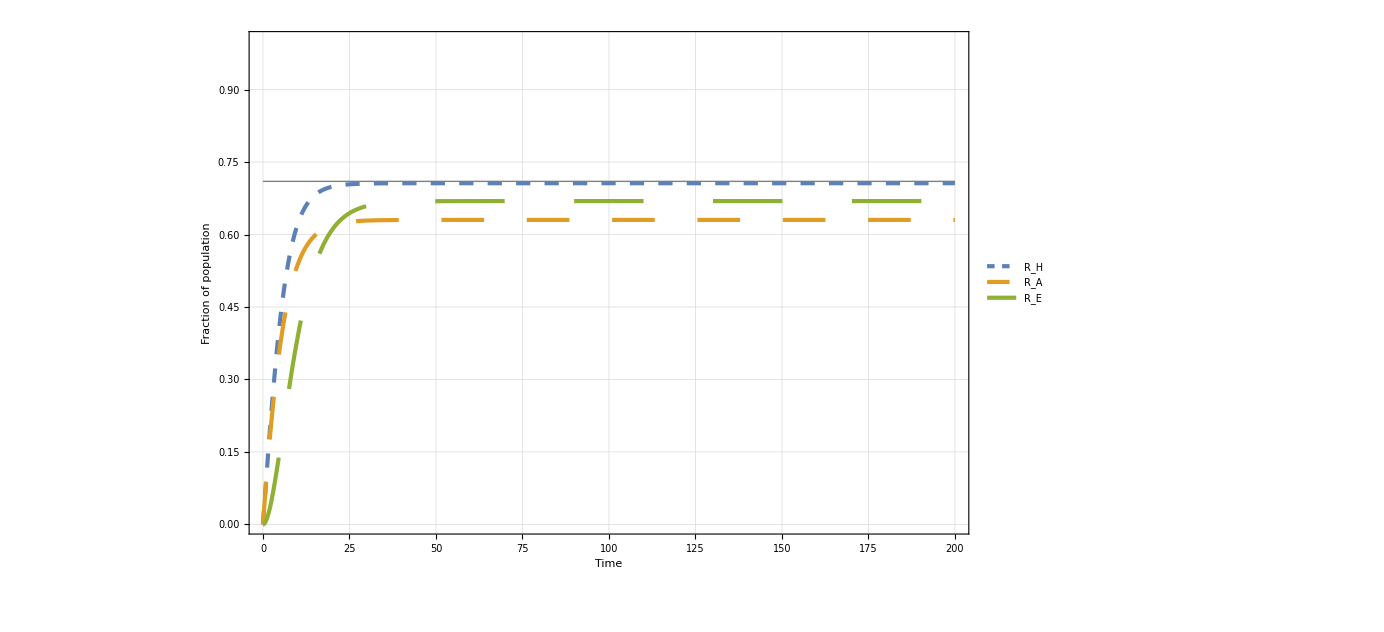

```mathematica
sol1 = NDSolve[{DiffUnbound/.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0}, {x,y, w}, {t, 0, 200}];
humantarget = Line[{{ 0, 0.71}, {200, 0.71}}];
Plot[{Evaluate[x[t]/.sol1[[1,1]]], Evaluate[y[t]/.sol1[[1,2]]], Evaluate[w[t]/.sol1[[1,3]]]}, {t,0,200}, PlotRange->{{0,200},{0.0,1.0}}, PlotStyle->{Dashing[0.01], Dashing[0.03], Dashing[0.05]},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All, ImageSize->1024, FrameLabel->{"Time", "Fraction of population"},PlotLegends->{"R_H", "R_A", "R_E"}, LabelStyle->Directive[Bold, Large], Prolog->{Directive[{Thick, Gray}], humantarget}, ImageSize->500]
```

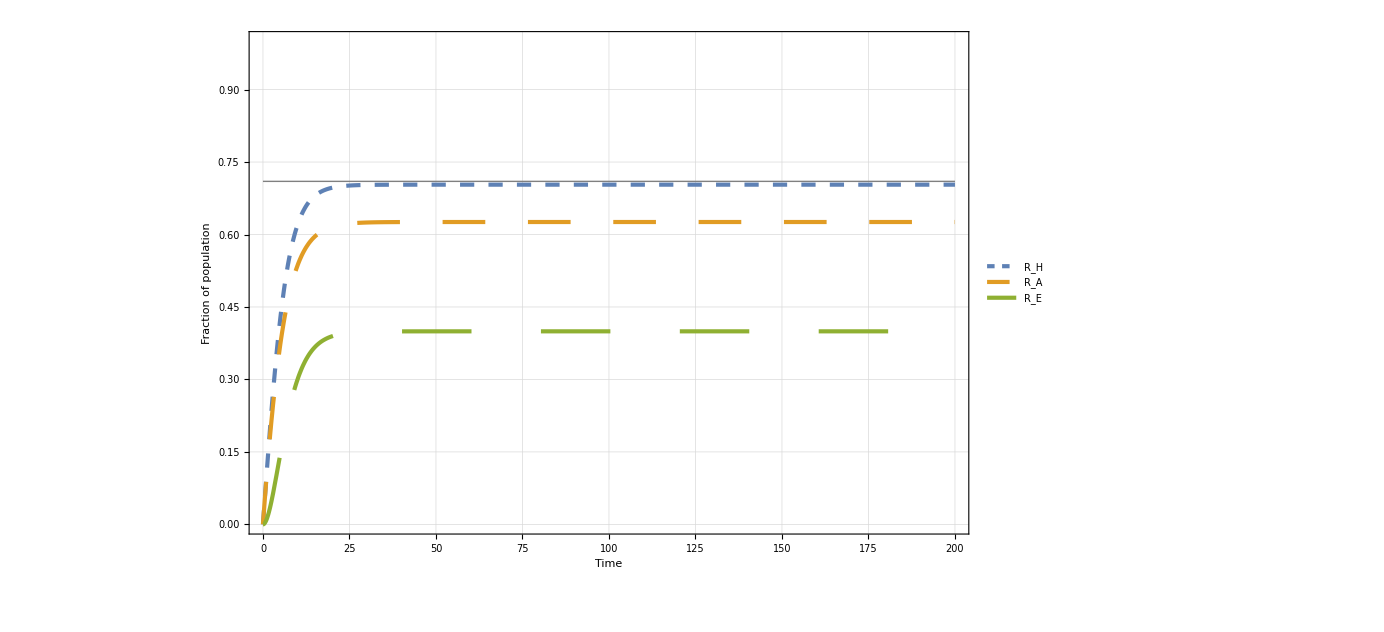

```mathematica
sol2 = NDSolve[{DiffBound/.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0}, {x,y, w}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol2[[1,1]]], Evaluate[y[t]/.sol2[[1,2]]], Evaluate[w[t]/.sol2[[1,3]]]}, {t,0,200}, PlotRange->{{0,200},{0.0,1.0}}, PlotStyle->{Dashing[0.01], Dashing[0.03], Dashing[0.05]},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All, ImageSize->1024, FrameLabel->{"Time", "Fraction of population"},PlotLegends->{"R_H", "R_A", "R_E"}, LabelStyle->Directive[Bold, Large],
Prolog->{Directive[{Thick, Gray}], humantarget}, ImageSize->500]
```

```mathematica
(*~~ 2. 3D plots {"β_EH","Λ_A", "R_H^*"} ~~*)
(*Plotting functions*)
EqSystem1 = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
```

```mathematica
NSolSys1[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betHA_,betAH_,betEH_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{EqSystem1[[1]]==0, EqSystem1[[2]]==0, EqSystem1[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals]
plot1env[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betHA_,betAH_,betEH_,betEA_,betHE_,betAE_,muH_,muA_,muE_] := Evaluate[NSolSys1[LamH,LamA,gamH,gamA,betHH,betAA,betAH,betEH,betHA,betEA,betHE,betAE,muH,muA,muE]][[1,1,2]]
```

```mathematica
(*scenario 1 *)
Plot3D[plot1env[0.1, par2, 1/1000, 1/1000, 0.2,0.1,0.001,0.001,par1,0.001,0.01,0.001, 0.1, 0.1, 0.2],{par1,0,1},{par2,0,1}, AxesLabel->{"β_EH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {0,0}, {0,1}}]
```

-Graphics3D-

```mathematica
(*scenario 2*)
Plot3D[plot1env[0.1, par2,1/1000, 1/1000, 0.1,0.1,0.05,0.05,par1,0.1,0.1,0.1, 0.1, 0.1, 0.2],{par1,0,1},{par2,0,1}, AxesLabel->{"β_EH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {0,0}, {0,1}}]
```

```mathematica
(*scenario 3*)
Plot3D[plot1env[0.1, par2,1/1000, 1/1000, 0.15,0.2,0.01,0.01,par1,0.01,0.01,0.01, 0.1, 0.1, 0.2],{par1,0,1},{par2,0,1}, AxesLabel->{"β_EH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange-> {{0,1},{0,1},{0.6,1.0}},
AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {0,0}, {0,1}}]
```

```mathematica
(*~~ 2. Solve ~~*)
(* Step 1. Use equations for RE and RA, assuming steady RH *)
ODESystem3 = {
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A] + Subscript[γ, H]*Subscript[Λ, H]+ Subscript[β, AE]*y[t] + Subscript[β, HE] * x - Subscript[μ, e]*w[t]
};
```

```mathematica
(* Step 2. Solve this system for equilibrium *)
sol2 = DSolve[{ODESystem3[[1]]==0, ODESystem3[[2]]==0}, {y,w},t, 
Assumptions->{Subscript[β, HA]≥ 0, Subscript[β, AA]≥ 0, Subscript[β, EA]≥ 0, Subscript[β, AE]≥ 0,Subscript[β, HE]≥ 0, Subscript[μ, e]≥ 0, Subscript[μ, A]≥ 0, x≥ 0, Subscript[γ, A]≥ 0, Subscript[γ, H]≥ 0, Subscript[Λ, A]≥ 0, Subscript[Λ, H]≥ 0}];
```

```mathematica
(*This gives us two solutions, with equations of quadratic form. We need to select the 'positive' solution.*)
(*Demonstrate for self satisfaction that we are working with quadratic functions *)
f[y_] := (1-y) * (0.1+0.1*0.7+0.1*y + 0.2 * 2)-0.1*y
Plot[f[w], {w, -10, 5}]
```

```mathematica
(* Step 3. Select correct solution. Have to plot the different solutions to look at what value they are suggesting*)
solv1 = sol2[[1]]; (*RA==0*)
solv2 = sol2[[2]]; (*RE==0*)
wv1 = Plot[Evaluate[w[t]/.solv1[[1]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
wv2 = Plot[Evaluate[w[t]/.solv2[[1]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
GraphicsRow[{wv1, wv2}]
yv1 = Plot[Evaluate[y[t]/.solv1[[2]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
yv2 = Plot[Evaluate[y[t]/.solv2[[2]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10,  x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]-> 0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}], {t,0,200}];
GraphicsRow[{yv1, yv2}]
(*Solution two is the (biologically speaking) right solution. Now Try to simplify.*)
```

```mathematica
(*Simplify to get a simpler equation*)
yorigeq = solv2[[2, 2, 2]]; (*eq found above*)
yeq= FullSimplify[yorigeq]; (*can we get a simper one?*)
```

```mathematica
worigeq = solv2[[1, 2, 2]];
weq = FullSimplify[worigeq];
```

```mathematica
(*Looking at plots with RH on one axis and RA or RE on the other, and looking at conseqence of different parameter combinations.*)
(*Define functions so that we can make plots*)
yfunc[xs_, bea_, bhe_, bae_, mue_, gA_, gH_, LA_, LH_ ] := yeq /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> bea, Subscript[Λ, A]-> 1/10, x->xs, Subscript[β, HE]->bhe, Subscript[β, AE]-> bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> gA, Subscript[γ, H]->gH, Subscript[Λ, A]-> LA, Subscript[Λ, H]-> LA};
wfunc[xs_,bea_, bhe_, bae_, mue_, gA_, gH_, LA_, LH_]:= weq/.{Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1bea, Subscript[Λ, A]-> 1/10, x->xs, Subscript[β, HE]->bhe, Subscript[β, AE]-> bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1,Subscript[γ, A]-> gA, Subscript[γ, H]->gH, Subscript[Λ, A]-> LA, Subscript[Λ, H]-> LA};
```

```mathematica
(*Can use a manipulate plot - but not on an i5*) (*Manipulate[Plot[{yfunc[par1, bea, bhe, bae, mue, Le], wfunc[par1, bea, bhe, bae, mue, Le]},{par1,0,1}, AxesLabel->{"R_H^*", "R^*"}, PlotRange->{{0,1},{0,3}}], {bea, 0, 1}, {bhe, 0, 1},{bae, 0, 1}, {mue, 0, 1.0}, {Le, 0, 0.1}]*)
```

```mathematica
(* Step 4. Solve analytical solutions for x*)
yeqx = Solve[yeq==y, x];(*x on right hand side*)
ytargfixedx= Solve[0.7 == yeqx[[1,1,2]], y]; (*for a given x, what par combinations/RA values are possible?*)
ytargfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1} (*find right solution*)
```

{{y→-2.21816},{y→0.723106}}⟦i,1,2⟧

```mathematica
yfixedxplot[La_, bHE_] :=Evaluate[ytargfixedx[[2,1,2]]/.{Subscript[Λ, A] -> La, Subscript[β, HE]-> bHE, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}]
```

```mathematica
Plot3D[yfixedxplot[par1,par2], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_A"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]]
```

```mathematica
weqx = Solve[{w == weq}, x];
weqx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1, w -> 2} (*which solution is positive?*)
```

{{x→16.7507},{x→-222.051}}⟦i,1,2⟧

```mathematica
wtargfixedx = Solve[0.7==weqx[[1,1,2]], w];
(*which solution is the right one*) 
wtargfixedx[[i,1,2]]/.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}
```

{{w→-1.03418},{w→0.954183}}⟦i,1,2⟧

```mathematica
wfixedxplot[La_, bHE_] :=Evaluate[wtargfixedx[[2,1,2]]/.{Subscript[Λ, A] -> La, Subscript[β, HE]-> bHE, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[γ, A]-> 0.1, Subscript[γ, H]->0.1, Subscript[Λ, A]-> 0.1, Subscript[Λ, H]-> 0.1}]
```

```mathematica
Plot3D[wfixedxplot[par1, par2], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_E"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]]
```

```mathematica
5
```

```mathematica
(*~~ 3. Equilibrium analysis for sensitivity analysis ~~*)
parameters = Rest[Import["M:\\New projects\\Model env compartment\\paramodel.csv"]];
```

```mathematica
ODESystemFASTUnbounded = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
equilibriumUnbounded[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betAH_,betEH_,betHA_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{ODESystemFASTUnbounded[[1]]==0, ODESystemFASTUnbounded[[2]]==0, ODESystemFASTUnbounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals][[1, 1, 2]]
```

```mathematica
eqanalysisUnbounded = Table[equilibriumUnbounded[parameters[[x, 2]], parameters[[x, 3]], parameters[[x, 4]], parameters[[x, 5]], parameters[[x, 6]], 
parameters[[x, 7]], parameters[[x, 8]], parameters[[x, 9]], parameters[[x, 10]],parameters[[x, 11]], parameters[[x, 12]], 
parameters[[x, 13]], parameters[[x, 14]], parameters[[x, 15]], parameters[[x,16]]],{x, 1, Length[parameters]}];
```

```mathematica
Export["M:\\New projects\\Model env compartment\\outcomeequilibriumUnbounded.csv", eqanalysisUnbounded];
```

```mathematica
ODESystemFASTBounded = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
(1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t]
};
equilibriumBounded[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betAH_,betEH_,betHA_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{ODESystemFASTBounded[[1]]==0, ODESystemFASTBounded[[2]]==0, ODESystemFASTBounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals][[1, 1, 2]]
```

```mathematica
eqanalysisBounded = Table[equilibriumBounded[parameters[[x, 2]], parameters[[x, 3]], parameters[[x, 4]], parameters[[x, 5]], parameters[[x, 6]], 
parameters[[x, 7]], parameters[[x, 8]], parameters[[x, 9]], parameters[[x, 10]],parameters[[x, 11]], parameters[[x, 12]], 
parameters[[x, 13]], parameters[[x, 14]], parameters[[x, 15]], parameters[[x,16]]],{x, 1, Length[parameters]}];
```

```mathematica
Export["M:\\New projects\\Model env compartment\\outcomeequilibriumBounded.csv", eqanalysisBounded];
```

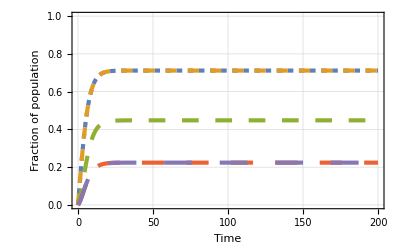

```mathematica
(*~~ 4. Fractions of RE contribution ~~*)
(*Trajectory plots*)
ODEboundfrac = {
x'[t] == Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t] == Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t] == (1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
z'[t] == (1-w[t]) * (Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
r'[t] == (1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
ODEunboundfrac = {
x'[t] == Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t] == Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t] == (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t],
z'[t] == (Subscript[γ, H]*Subscript[Λ, H] +Subscript[β, HE] * x[t]) - Subscript[μ, e]*z[t],
r'[t] == (Subscript[γ, A]*Subscript[Λ, A] +Subscript[β, AE] * y[t]) - Subscript[μ, e]*r[t]
};
sol3 = NDSolve[{ODEboundfrac/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol3[[1,1]]], Evaluate[y[t]/.sol3[[1,2]]], Evaluate[w[t]/.sol3[[1,3]]], Evaluate[z[t]/.sol3[[1,4]]], Evaluate[r[t]/.sol3[[1,5]]]}, {t,0,200}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,200},{0.0,1.0}},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

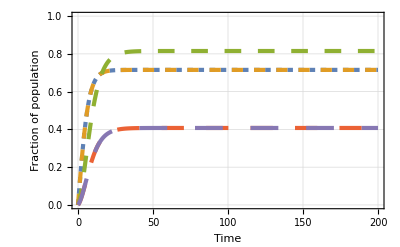

```mathematica
sol4 = NDSolve[{ODEunboundfrac/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 200}];
Plot[{Evaluate[x[t]/.sol4[[1,1]]], Evaluate[y[t]/.sol4[[1,2]]], Evaluate[w[t]/.sol4[[1,3]]], Evaluate[z[t]/.sol4[[1,4]]], Evaluate[r[t]/.sol4[[1,5]]]}, {t,0,200}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,200},{0.0,1.0}},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

```mathematica
(*functionc for plotting solutions*)
unboundsol1[bAE_, LA_, bEH_, bEA_] :=NSolve[{Unboundfrac[[1]]==0., Unboundfrac[[2]]==0., Unboundfrac[[3]]==0., Unboundfrac[[4]]==0., Unboundfrac[[5]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0. && z[t] ≥ 0. && r[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
boundsol1[bAE_, LA_, bEH_, bEA_] := NSolve[{Boundfrac[[1]]==0., Boundfrac[[2]]==0., Boundfrac[[3]]==0., Boundfrac[[4]]==0., Boundfrac[[5]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0. && z[t] ≥ 0. && r[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
getFrac[n_, sol_] := sol[[1,n,2]] 
HAratio[sol_] := sol[[1,5,2]]/sol[[1,4,2]]
```

```mathematica
(*try looking at the impact - functions*)
RCHbf[bAE_, bEH_, bEA_]:= boundsol1[bAE,0., bEH, bEA][[1,1,2]]
RCHuf[bAE_, bEH_, bEA_] := unboundsol1[bAE,0., bEH, bEA][[1,1,2]]
RHbf[bAE_, LA_, bEH_, bEA_]:= boundsol1[bAE,LA, bEH, bEA][[1,1,2]]
RHuf[bAE_, LA_, bEH_, bEA_] := unboundsol1[bAE,LA, bEH, bEA][[1,1,2]]
impact[RH_, RCH_] := 1 - (RCH/RH)
```

```mathematica
(*plot impact for changes in bAE*)
URHimpactmidEH = ContourPlot[impact[ RHuf[par1, par2, 1/100, 1/100], RCHuf[par1, 1/100, 1/100]],{par1,0.,5.},{par2,0.,1.}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All];
BRHimpactmidEH = ContourPlot[impact[RHbf[par1, par2, 1/100, 1/100], RCHbf[par1, 1/100, 1/100]],{par1,0.,1.},{par2,0.,1.}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All];
```

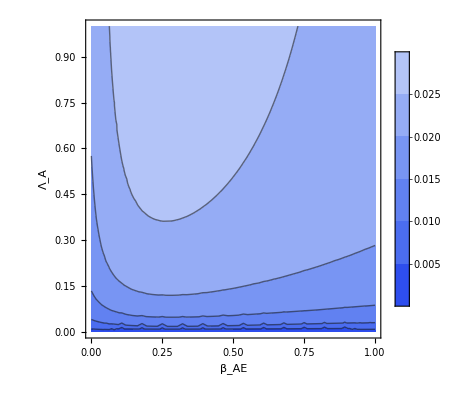
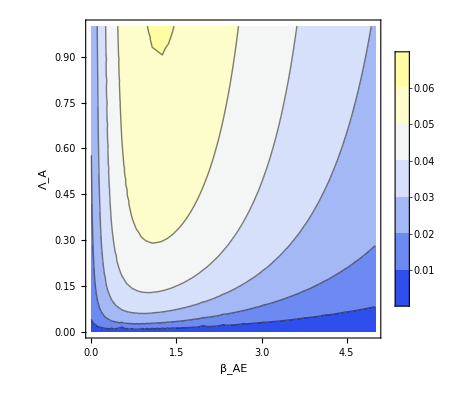
Row[-Graphics-,-Graphics-]

```mathematica
Row[BRHimpactmidEH,URHimpactmidEH] 
(*Row[BRHimpactmidEH,BRHimpactnoEH] 
Row[URHimpactmidEH, URHimpactnoEH]*)
```

```mathematica
(*plot impact for changes in bEH*)
URHimpactvarEH = ContourPlot[impact[ RHuf[1/10, par2, par1, 1/100], RCHuf[1/10, par1, 1/100]],{par1,0.,2.},{par2,0.,1.}, PlotLegends->Automatic, FrameLabel->{"β_EH","Λ_A"},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.2}}], PlotRange -> All];
BRHimpactvarEH = ContourPlot[impact[RHbf[1/10, par2, par1, 1/100], RCHbf[1/10, par1, 1/100]],{par1,0.,2.},{par2,0.,1.}, PlotLegends->Automatic, FrameLabel->{"β_EH","Λ_A"},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.2}}], PlotRange -> All];
```

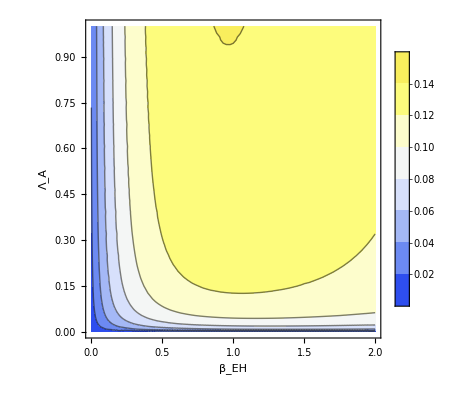
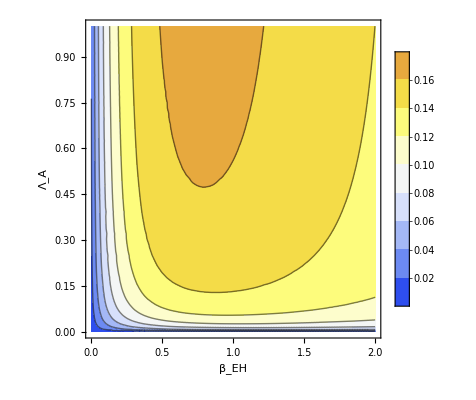
Row[-Graphics-,-Graphics-]

```mathematica
Row[BRHimpactvarEH,URHimpactvarEH]
```

```mathematica
(*~~ 5. How does curtailing ABx in animals affect and the controbution fo the environment to humans impact RH? ~~*)
```

```mathematica
bAE_, LA_, bEH_, bEA
```

```mathematica
(*Plot fraction of environment from animals*)
CPUREA = ContourPlot[unboundsol1[x, y, 1/100, 1/100][[1,5,2]],{x,0,0.2},{y,0.,1.}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 1.}}]];
CPBREA  = ContourPlot[boundsol1[x, y, 1/100, 1/100][[1,5,2]],{x,0,0.2},{y,0.,1.}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"}, LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 1.}}]];
(*UmidEHhighHA = ContourPlot[unboundHAsol[par1, par2, 1/10, 1/100, 1/100, 1/10][[1,5,2]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"},  LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0, 6}}]];
BmidEHhighHA = ContourPlot[boundHAsol[par1, par2, 1/10, 1/100, 1/100, 1/10][[1,5,2]],{par1,0,1},{par2,0,1}, PlotLegends->Automatic, FrameLabel->{"β_AE","Λ_A"}, LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0, 1}}]];*)
```

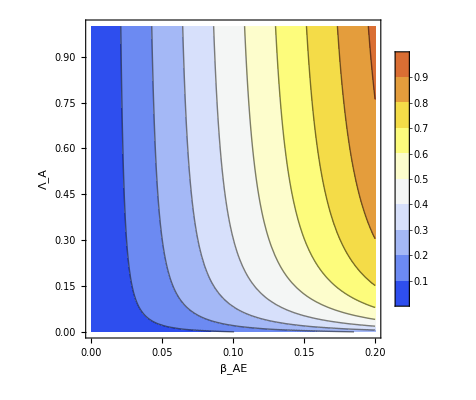
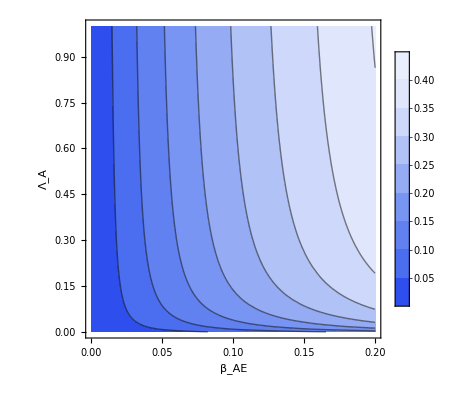
Row[-Graphics-,-Graphics-]

```mathematica
Row[CPUREA, CPBREA]
```

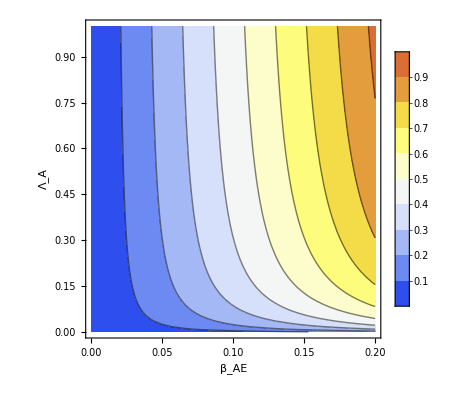
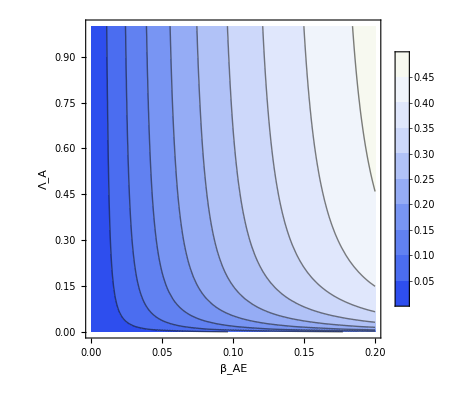
Row[-Graphics-,-Graphics-]

```mathematica
Row[CPUREA, CPBREA]
(*Row[BmidEHlowHA,BmidEHhighHA]*)
```

```mathematica
(* ---- 6. Changes to forces of infection ---- *)
(*Get force of infection from animals*)
FOIA[x_, y_, bAH_] :=bAH * y * (1-x)
(*Get force of infection from the environment*)
FOIE[x_, w_, bEH_] :=bEH * w * (1-x)
(*Get force of infection from other humans*)
FOIH[x_,  bHH_] :=bHH * x * (1-x)
(*Get force of infection from antibiotic usage*)
FOIab[x_, LH_] := LH * (1 - x)
```

```mathematica
(*Get RH for different environment structures based on bAH, bEH, bHH and LA*)
unboundsol[ LA_, bAH_, bEH_, bHH_] :=NSolve[{ODEunboundfracnondiff[[1]]==0, ODEunboundfracnondiff[[2]]==0, ODEunboundfracnondiff[[3]]==0, ODEunboundfracnondiff[[4]]==0, ODEunboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/1000, Subscript[β, AH]->bAH,Subscript[β, HH]-> bHH, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
boundsol[ LA_, bAH_, bEH_, bHH_] := NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/1000, Subscript[β, AH]->bAH,Subscript[β, HH]-> bHH, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
```

```mathematica
(*Get equilibrium values for different LA*)
xyw = Table[Table[boundsol[p1, 1/100, 1/100, 1/10][[1,n,2]], {n, 3}], {p1, {1.0, 0.67, 0.33, 0.0}}];
xywU = Table[Table[unboundsol[p1, 1/100, 1/100, 1/10][[1,n,2]], {n, 3}], {p1, {1.0, 0.67, 0.33, 0.0}}];
(*Get forces of infection*)
FOITab = Table[{FOIA[xyw[[row, 1]], xyw[[row, 2]], 1/10], FOIE[xyw[[row, 1]], xyw[[row, 3]],1/10], FOIH[xyw[[row,1]], 1/10], FOIab[xyw[[row, 1]], 1/10]}, {row, 4}] ;
FOITabU = Table[{FOIA[xywU[[row, 1]], xywU[[row, 2]], 1/10], FOIE[xywU[[row, 1]], xywU[[row, 3]],1/10], FOIH[xywU[[row,1]], 1/10], FOIab[xywU[[row, 1]], 1/10]}, {row, 4}] ;
(*Get proportions*)
sums = Table[Sum[FOITab[[n,i]],{i,4}], {n,4}];
props = Table[Table[FOITab[[n,i]]/sums[[n]], {i,4}], {n,4}];
sumsU = Table[Sum[FOITabU[[n,i]],{i,4}], {n,4}];
propsU = Table[Table[FOITabU[[n,i]]/sumsU[[n]], {i,4}], {n,4}];
```

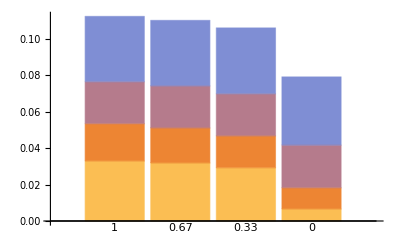
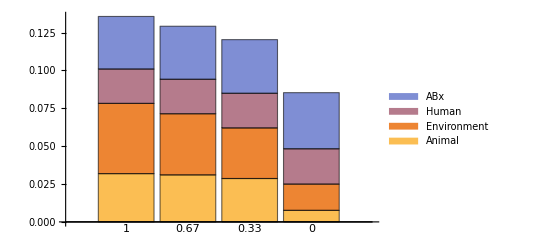
Row[-Graphics-,-Graphics-]

```mathematica
Row[BarChart[FOITab,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}],
BarChart[FOITabU,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal", "Environment","Human", "ABx"}]]
```

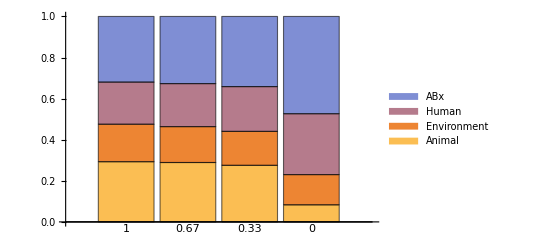
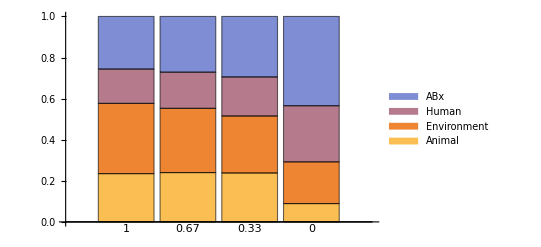
Row[-Graphics-,-Graphics-]

```mathematica
Row[BarChart[props,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal", "Environment","Human", "ABx"}],
BarChart[propsU,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal", "Environment","Human", "ABx"}]]
```

```mathematica
(*Get forces of infection for animals*)
ABconsumption = {1.0, 0.67, 0.33, 0.0}
FOITabAnimal = Table[{FOIA[xyw[[row, 2]], xyw[[row, 2]], 1/10], FOIE[xyw[[row, 2]], xyw[[row, 3]],1/10], FOIA[xyw[[row,2]], xyw[[row, 1]], 1/10], FOIab[xyw[[row, 2]], ABconsumption[[row]]]}, {row, 4}] ;
FOITabUAnimal = Table[{FOIA[xywU[[row, 2]], xywU[[row, 2]], 1/10], FOIE[xywU[[row, 2]], xywU[[row, 3]],1/10], FOIA[xywU[[row,2]], xywU[[row, 1]], 1/10], FOIab[xywU[[row, 2]], ABconsumption[[row]]]}, {row, 4}] ;
(*Get proportions*)
sumsAnimal = Table[Sum[FOITabAnimal[[n,i]],{i,4}], {n,4}];
propsAnimal = Table[Table[FOITabAnimal[[n,i]]/sumsAnimal[[n]], {i,4}], {n,4}];
sumsUAnimal = Table[Sum[FOITabUAnimal[[n,i]],{i,4}], {n,4}];
propsUAnimal = Table[Table[FOITabUAnimal[[n,i]]/sumsUAnimal[[n]], {i,4}], {n,4}];
```

{1.,0.67,0.33,0.}

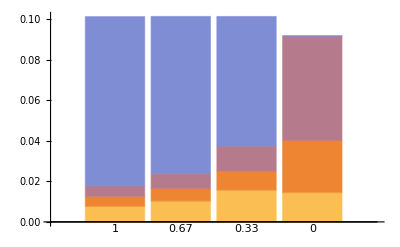
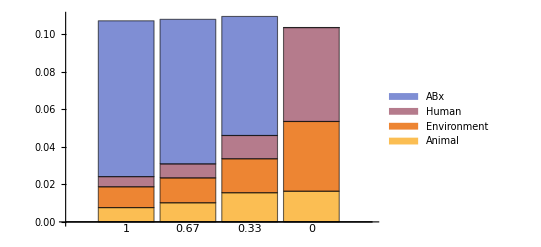
Row[-Graphics-,-Graphics-]

```mathematica
Row[BarChart[FOITabAnimal,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}],
BarChart[FOITabUAnimal,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal", "Environment","Human", "ABx"}]]
```

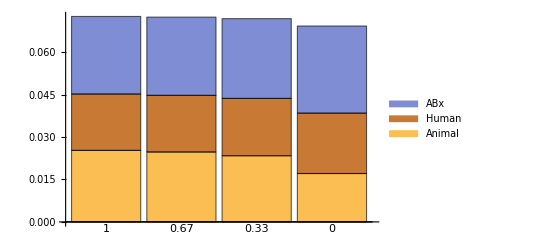
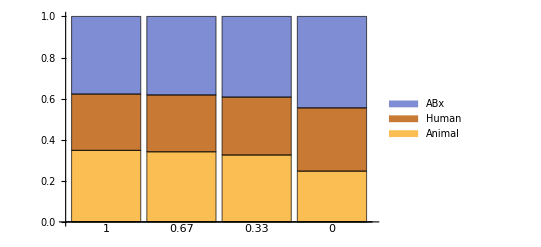
Row[-Graphics-,-Graphics-]

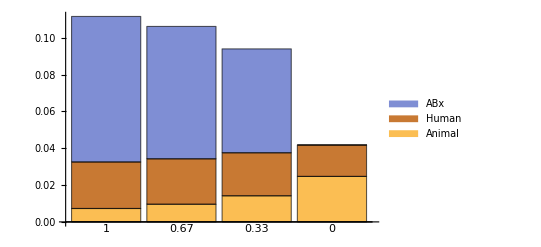
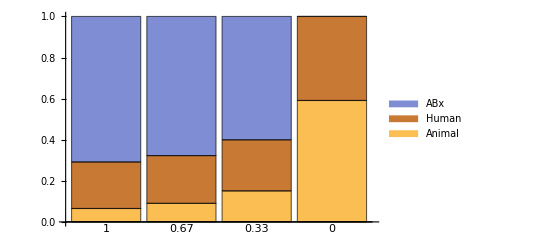
Row[-Graphics-,-Graphics-]

```mathematica
(*Compare to two compartment model*)
bound2compsol[ LA_, bAH_, bEH_, bHH_] := NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10, Subscript[β, AH]->bAH,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> 0, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]->1/10, Subscript[γ, H]->1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
(*Get equilibrium values for different LA*)
xyw2c = Table[Table[bound2compsol[p1, 1/10, 0, 1/10][[1,n,2]], {n, 3}], {p1, {1.0, 0.67, 0.33, 0.0}}];
(*Get forces of infection*)
FOITab2comp = Table[{FOIA[xyw2c[[row, 1]], xyw2c[[row, 2]], 1/10], FOIH[xyw2c[[row,1]], 1/10], FOIab[xyw2c[[row, 1]], 1/10]}, {row, 4}] ;
(*Get proportions*)
sums2c = Table[Sum[FOITab2comp[[n,i]],{i,3}], {n,4}];
props2c = Table[Table[FOITab2comp[[n,i]]/sums2c[[n]], {i,3}], {n,4}];
(*Get forces of infection for animals*)
FOITab2compAnimal = Table[{FOIA[xyw2c[[row, 2]], xyw2c[[row, 2]], 1/10], FOIA[xyw2c[[row,1]],xyw2c[[row, 2]],  1/10], FOIab[xyw2c[[row, 2]], ABconsumption[[row]]]}, {row, 4}] ;
(*Get proportions*)
sums2cAnimal = Table[Sum[FOITab2compAnimal[[n,i]],{i,3}], {n,4}];
props2cAnimal = Table[Table[FOITab2compAnimal[[n,i]]/sums2cAnimal[[n]], {i,3}], {n,4}];
Row[BarChart[FOITab2comp,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal","Human", "ABx"}],
BarChart[props2c,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal","Human", "ABx"}]]
Row[BarChart[FOITab2compAnimal,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal","Human", "ABx"}],
BarChart[props2cAnimal,ChartLayout->"Stacked",ChartLabels->{{1, 0.67, 0.33,0},None}, ChartLegends->{"Animal","Human", "ABx"}]]
```

```mathematica
xyw2c
```

{{0.72578,0.920928,0.733099},{0.72346,0.892659,0.704677},{0.718076,0.828974,0.664097},{0.692021,0.554958,0.57392}}

```mathematica
(* ---- 7. Trajectory plots - what happens just after an intervention of animal ABx has been implemented? ---- *)
(*Get equilibrium values for Subscript[Λ, A]=0.1*) 
solest = NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10000,Subscript[β, AH]->1/100,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 9/100, Subscript[β, EA]-> 9/10000, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1,Subscript[Λ, H]->1/10, Subscript[γ, A]->1/10, Subscript[γ, H]->1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals];
RH := solest[[1,1,2]];
RA := solest[[1,2,2]];
RE := solest[[1,3,2]];
REh := solest[[1,4,2]];
REa := solest[[1,5,2]];
solest2 = NSolve[{ODEunboundfracnondiff[[1]]==0, ODEunboundfracnondiff[[2]]==0, ODEunboundfracnondiff[[3]]==0, ODEunboundfracnondiff[[4]]==0, ODEunboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/10000,Subscript[β, AH]->1/100,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 9/100, Subscript[β, EA]-> 9/10000, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1,Subscript[Λ, H]->1/10, Subscript[γ, A]->1/10, Subscript[γ, H]->1/10}, {x[t], y[t], w[t], z[t], r[t]}, Reals];
RHu := solest2[[1,1,2]];
RAu := solest2[[1,2,2]];
REu := solest2[[1,3,2]];
REhu := solest2[[1,4,2]];
REau := solest2[[1,5,2]];
solest3 = NSolve[{ODEboundfracnondiff[[1]]==0, ODEboundfracnondiff[[2]]==0, ODEboundfracnondiff[[3]]==0, ODEboundfracnondiff[[4]]==0, ODEboundfracnondiff[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t] ≥ 0 && r[t] ≥ 0} /.{Subscript[β, HA]->1/1000, Subscript[β, AH]->1/10,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1, Subscript[γ, A]->0, Subscript[γ, H]->0}, {x[t], y[t], w[t], z[t], r[t]}, Reals];
RH2 := solest3[[1,1,2]];
RA2 := solest3[[1,2,2]];
RE2 := solest3[[1,3,2]];
REh2 :=0;
REa2 := 0;
```

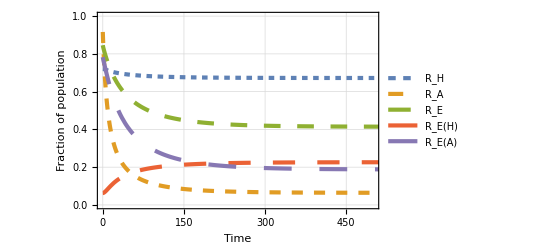
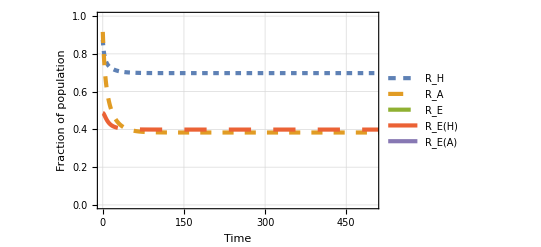
Row[-Graphics-,-Graphics-]

```mathematica
sol3 = NDSolve[{ODEboundfrac/.
{Subscript[β, HA]->1/10000,Subscript[β, AH]->1/100,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 9/100, Subscript[β, EA]-> 9/10000, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == RH, y[0]== RA, w[0]==RE, z[0] == REh, r[0] == REa}, {x,y, w, z, r}, {t, 0, 1000}];
Row[Plot[{Evaluate[x[t]/.sol3[[1,1]]], Evaluate[y[t]/.sol3[[1,2]]], Evaluate[w[t]/.sol3[[1,3]]], Evaluate[z[t]/.sol3[[1,4]]], Evaluate[r[t]/.sol3[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]],Plot[{Evaluate[x[t]/.sol4[[1,1]]], Evaluate[y[t]/.sol4[[1,2]]], Evaluate[w[t]/.sol4[[1,3]]], Evaluate[z[t]/.sol4[[1,4]]], Evaluate[r[t]/.sol4[[1,5]]]}, {t,0,2000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"}, PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]]
```

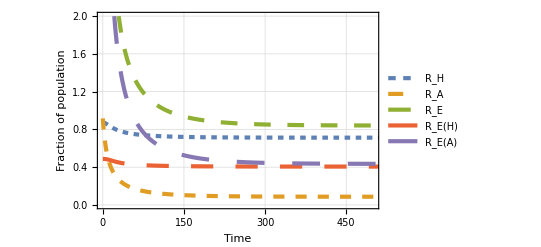

```mathematica
sol4 = NDSolve[{ODEunboundfrac/.{Subscript[β, HA]->1/10000,Subscript[β, AH]->1/100,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 9/100, Subscript[β, EA]-> 9/10000, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/10, Subscript[γ, H]-> 1/10}, x[0] == RHu, y[0]== RAu, w[0]==REu, z[0] == REhu, r[0] == REau}, {x,y, w, z, r}, {t, 0, 1000}];
Plot[{Evaluate[x[t]/.sol4[[1,1]]], Evaluate[y[t]/.sol4[[1,2]]], Evaluate[w[t]/.sol4[[1,3]]], Evaluate[z[t]/.sol4[[1,4]]], Evaluate[r[t]/.sol4[[1,5]]]}, {t,0,2000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,2.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"}, PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

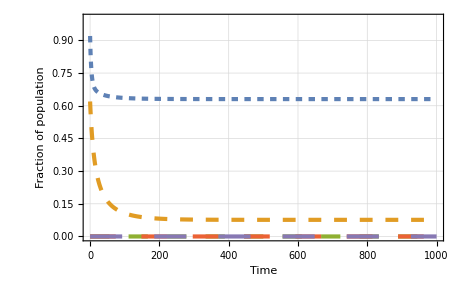

```mathematica
sol4 = NDSolve[{ODEunboundfrac/.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 0, Subscript[γ, H]->0}, x[0] == RH2, y[0]== RA2, w[0]==RE2, z[0] == REh2, r[0] == REa2}, {x,y, w, z, r}, {t, 0, 1000}];
Plot[{Evaluate[x[t]/.sol4[[1,1]]], Evaluate[y[t]/.sol4[[1,2]]], Evaluate[w[t]/.sol4[[1,3]]], Evaluate[z[t]/.sol4[[1,4]]], Evaluate[r[t]/.sol4[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,1000},{0.0,1.0}},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

```mathematica
RA
```

0.618807

```mathematica
(* ~~ is the number of compartments or the connectivity between them more important? ~~ *)

(*Table of parameters - created in a csv *)
parameters = Import["M:\\New projects\\Model env compartment\\unevensharetransmission_para.csv"];
```

```mathematica
(*sets of equations*)
ODESystemFASTUnbounded = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
ODESystemFASTBounded = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
(1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t]
};
```

```mathematica
(*equations to get eqlm values*)
equilibriumUnbounded[bHA_,bAH_,bHH_,bAA_,bEH_,bEA_,bHE_,bAE_,mA_,mH_,mE_,LA_,LH_,gA_,gH_]:= NSolve[{ODESystemFASTUnbounded[[1]]==0, ODESystemFASTUnbounded[[2]]==0, ODESystemFASTUnbounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[β, HA]->bHA,Subscript[β, AH]->bAH,Subscript[β, HH]->bHH, Subscript[β, AA]-> bAA,Subscript[β, EH] -> bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->mA,Subscript[μ, H]->mH, Subscript[μ, e] -> mE, Subscript[Λ, A]->LA,Subscript[Λ, H]->LH, Subscript[γ, A]-> gA, Subscript[γ, H]->gH}, {x[t], y[t], w[t]}, Reals][[1, 1, 2]]
equilibriumBounded[bHA_,bAH_,bHH_,bAA_,bEH_,bEA_,bHE_,bAE_,mA_,mH_,mE_,LA_,LH_,gA_,gH_]:= NSolve[{ODESystemFASTBounded[[1]]==0, ODESystemFASTBounded[[2]]==0, ODESystemFASTBounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[β, HA]->bHA,Subscript[β, AH]->bAH,Subscript[β, HH]->bHH, Subscript[β, AA]-> bAA,Subscript[β, EH] -> bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->mA,Subscript[μ, H]->mH, Subscript[μ, e] -> mE, Subscript[Λ, A]->LA,Subscript[Λ, H]->LH, Subscript[γ, A]-> gA, Subscript[γ, H]->gH}, {x[t], y[t], w[t]}, Reals][[1, 1, 2]]
```

```mathematica
eqanalysisUnbounded = Table[equilibriumUnbounded[parameters[[x, 1]], parameters[[x, 2]], parameters[[x, 3]], parameters[[x, 4]], parameters[[x, 5]], 
parameters[[x, 6]], parameters[[x, 7]], parameters[[x, 8]], parameters[[x, 9]],parameters[[x, 10]], parameters[[x, 11]], 
parameters[[x, 12]], parameters[[x, 13]], parameters[[x, 14]], parameters[[x,15]]],{x, 1, Length[parameters]}];
eqanalysisBounded = Table[equilibriumBounded[parameters[[x, 1]], parameters[[x, 2]], parameters[[x, 3]], parameters[[x, 4]], parameters[[x, 5]], 
parameters[[x, 6]], parameters[[x, 7]], parameters[[x, 8]], parameters[[x, 9]],parameters[[x, 10]], parameters[[x, 11]], 
parameters[[x, 12]], parameters[[x, 13]], parameters[[x, 14]], parameters[[x,15]]],{x, 1, Length[parameters]}];
```

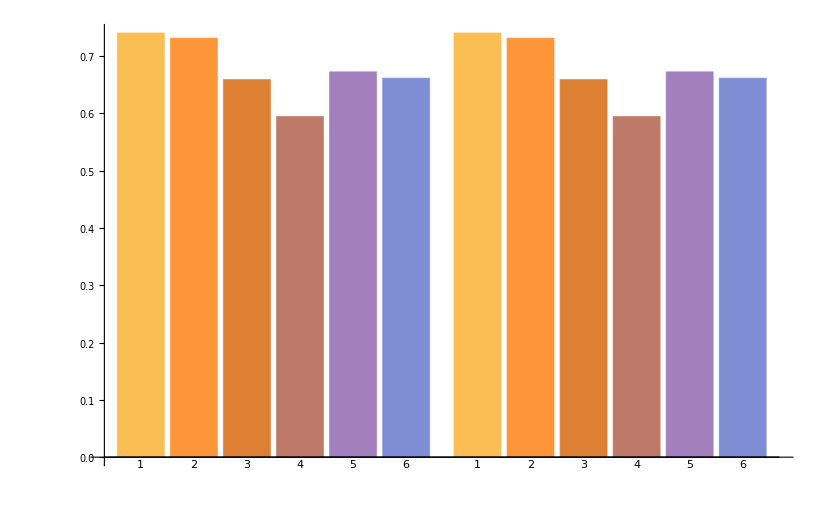

```mathematica
BarChart[{eqanalysisBounded, eqanalysisBounded},ChartLayout -> "Grouped",ChartLabels->{1,2,3,4,5,6}]
```

```mathematica
(* environmental transmission parameters against impact line plots *)
```

```mathematica
(*sets of equations*)
ODESystemU = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
ODESystemB = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
(1-w[t]) * (Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t]) - Subscript[μ, e]*w[t]
};
```

```mathematica
(*functionc for plotting solutions*)
unboundsol2[LA_, bEH_, bEA_, bHE_, bAE_] :=NSolve[{ODESystemU[[1]]==0., ODESystemU[[2]]==0., ODESystemU[[3]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/100,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals]
boundsol2[LA_, bEH_, bEA_, bHE_, bAE_] := NSolve[{ODESystemB[[1]]==0., ODESystemB[[2]]==0., ODESystemB[[3]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/100,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals]
```

```mathematica
(*try looking at the impact - functions*)
RCHbf[bEH_, bEA_, bHE_, bAE_]:= boundsol2[0., bEH, bEA, bHE, bAE][[1,1,2]]
RCHuf[bEH_, bEA_, bHE_, bAE_] := unboundsol2[0., bEH, bEA, bHE, bAE][[1,1,2]]
RHbf[LA_, bEH_, bEA_, bHE_, bAE_]:= boundsol2[LA, bEH, bEA, bHE, bAE][[1,1,2]]
RHuf[LA_, bEH_, bEA_, bHE_, bAE_] := unboundsol2[LA, bEH, bEA, bHE, bAE][[1,1,2]]
impact[RH_, RCH_] := 1 - (RCH/RH)
```

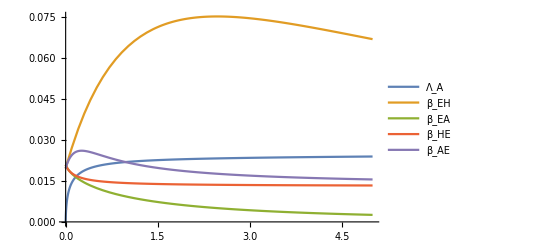

```mathematica
Plot[{impact[RHbf[par1, 1/100, 1/100, 1/100, 1/100], RCHbf[1/100, 1/100, 1/100, 1/100]],
impact[RHbf[0.5, par1, 1/100, 1/100, 1/100], RCHbf[par1, 1/100, 1/100, 1/100]], 
impact[RHbf[0.5, 1/100, par1, 1/100, 1/100], RCHbf[1/100, par1, 1/100, 1/100]], 
impact[RHbf[0.5, 1/100, 1/100,par1, 1/100], RCHbf[1/100, 1/100,par1, 1/100]], 
impact[RHbf[0.5, 1/100, 1/100, 1/100, par1], RCHbf[1/100, 1/100, 1/100, par1]]},{par1, 0., 5.},
PlotLegends-> {"Λ_A","β_EH", "β_EA", "β_HE", "β_AE"}]
```

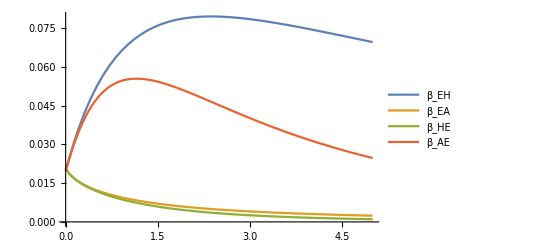

```mathematica
Plot[{
impact[RHuf[0.5, par1, 1/100, 1/100, 1/100], RCHuf[par1, 1/100, 1/100, 1/100]], 
impact[RHuf[0.5, 1/100, par1, 1/100, 1/100], RCHuf[1/100, par1, 1/100, 1/100]], 
impact[RHuf[0.5, 1/100, 1/100,par1, 1/100], RCHuf[1/100, 1/100,par1, 1/100]], 
impact[RHuf[0.5, 1/100, 1/100, 1/100, par1], RCHuf[1/100, 1/100, 1/100, par1]]},{par1, 0., 5.},
PlotLegends-> {"β_EH", "β_EA", "β_HE", "β_AE"}]
```

```mathematica
(*lambda A reductions vs evironmental parameter reductions*)
```

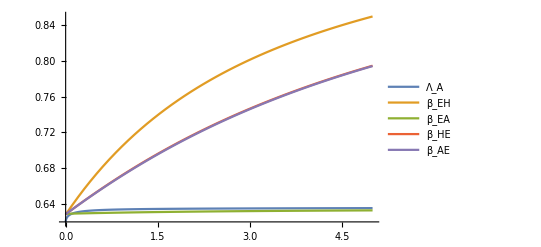

```mathematica
Plot[
{RHuf[par1, 1/100, 1/100, 1/100, 1/100],
RHuf[1/10, par1, 1/100, 1/100, 1/100], 
RHuf[1/10, 1/100, par1, 1/100, 1/100], 
RHuf[1/10, 1/100, 1/100,par1, 1/100], 
RHuf[1/10, 1/100, 1/100, 1/100, par1]},
{par1, 0., 5.},
PlotLegends-> {"Λ_A","β_EH", "β_EA", "β_HE", "β_AE"}]
```

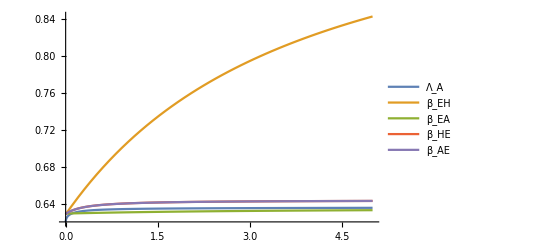

```mathematica
Plot[
{RHbf[par1, 1/100, 1/100, 1/100, 1/100],
RHbf[1/10, par1, 1/100, 1/100, 1/100], 
RHbf[1/10, 1/100, par1, 1/100, 1/100], 
RHbf[1/10, 1/100, 1/100,par1, 1/100], 
RHbf[1/10, 1/100, 1/100, 1/100, par1]},
{par1, 0., 5.},
PlotLegends-> {"Λ_A","β_EH", "β_EA", "β_HE", "β_AE"}, PlotRange->All]
```

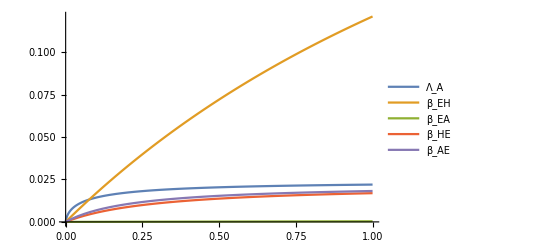

```mathematica
Plot[{
impact[RHbf[par1, 1/100, 1/100, 1/100, 1/100], RHbf[0., 1/100, 1/100, 1/100, 1/100]],
impact[RHbf[0.5, par1, 1/100, 1/100, 1/100], RHbf[0.5, 0., 1/100, 1/100, 1/100]], 
impact[RHbf[0.5, 1/100, par1, 1/100, 1/100], RHbf[0.5, 1/100, 0., 1/100, 1/100]], 
impact[RHbf[0.5, 1/100, 1/100,par1, 1/100], RHbf[0.5, 1/100, 1/100,0., 1/100]], 
impact[RHbf[0.5, 1/100, 1/100, 1/100, par1], RHbf[0.5, 1/100, 1/100, 1/100, 0.]]},{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH", "β_EA", "β_HE", "β_AE"}, PlotRange->All]
```

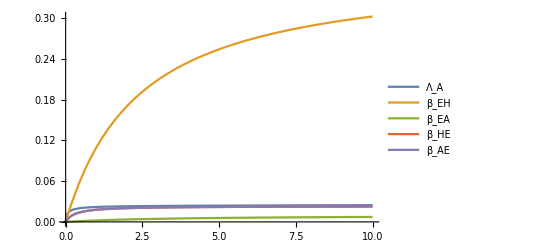

```mathematica
Plot[{
impact[RHbf[par1, 1/100, 1/100, 1/100, 1/100], RHbf[0., 1/100, 1/100, 1/100, 1/100]],
impact[RHbf[0.1, par1, 1/100, 1/100, 1/100], RHbf[0.1, 0., 1/100, 1/100, 1/100]], 
impact[RHbf[0.1, 1/100, par1, 1/100, 1/100], RHbf[0.1, 1/100, 0., 1/100, 1/100]], 
impact[RHbf[0.1, 1/100, 1/100,par1, 1/100], RHbf[0.1, 1/100, 1/100,0., 1/100]], 
impact[RHbf[0.1, 1/100, 1/100, 1/100, par1], RHbf[0.1, 1/100, 1/100, 1/100, 0.]]},{par1, 0., 10.},
PlotLegends-> {"Λ_A","β_EH", "β_EA", "β_HE", "β_AE"}, PlotRange->All]
```

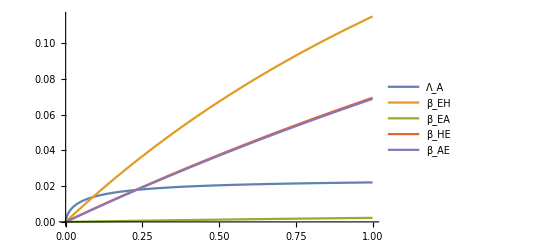

```mathematica
Plot[{
impact[RHuf[par1, 1/100, 1/100, 1/100, 1/100], RHuf[0., 1/100, 1/100, 1/100, 1/100]],
impact[RHuf[0.1, par1, 1/100, 1/100, 1/100], RHuf[0.1, 0., 1/100, 1/100, 1/100]], 
impact[RHuf[0.1, 1/100, par1, 1/100, 1/100], RHuf[0.1, 1/100, 0., 1/100, 1/100]], 
impact[RHuf[0.1, 1/100, 1/100,par1, 1/100], RHuf[0.1, 1/100, 1/100,0., 1/100]], 
impact[RHuf[0.1, 1/100, 1/100, 1/100, par1], RHuf[0.1, 1/100, 1/100, 1/100, 0.]]},{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH", "β_EA", "β_HE", "β_AE"}, PlotRange->All]
```

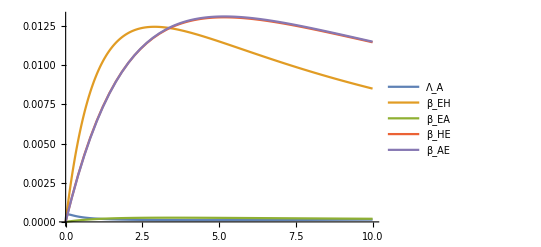

```mathematica
Plot[{
impact[RHuf[par1, 1/100, 1/100, 1/100, 1/100], RHuf[par1*0.9, 1/100, 1/100, 1/100, 1/100]],
impact[RHuf[0.1, par1, 1/100, 1/100, 1/100], RHuf[0.1, par1*0.9, 1/100, 1/100, 1/100]], 
impact[RHuf[0.1, 1/100, par1, 1/100, 1/100], RHuf[0.1, 1/100, par1*0.9, 1/100, 1/100]], 
impact[RHuf[0.1, 1/100, 1/100,par1, 1/100], RHuf[0.1, 1/100, 1/100,par1*0.9, 1/100]], 
impact[RHuf[0.1, 1/100, 1/100, 1/100, par1], RHuf[0.1, 1/100, 1/100, 1/100, par1*0.9]]},{par1, 0., 10.},
PlotLegends-> {"Λ_A","β_EH", "β_EA", "β_HE", "β_AE"}, PlotRange->All]
```

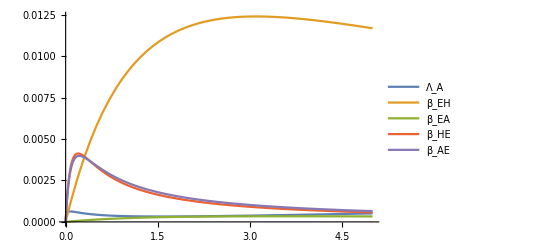

```mathematica
Plot[{
impact[RHbf[par1, 1/10, 1/100, 1/100, 1/100], RHbf[par1*0.9, 1/10, 1/100, 1/100, 1/100]],
impact[RHbf[0.1, par1, 1/100, 1/100, 1/100], RHbf[0.1, par1*0.9, 1/100, 1/100, 1/100]], 
impact[RHbf[0.1, 1/10, par1, 1/100, 1/100], RHbf[0.1, 1/10, par1*0.9, 1/100, 1/100]], 
impact[RHbf[0.1, 1/10, 1/100,par1, 1/100], RHbf[0.1, 1/10, 1/100,par1*0.9, 1/100]], 
impact[RHbf[0.1, 1/10, 1/100, 1/100, par1], RHbf[0.1, 1/10, 1/100, 1/100, par1*0.9]]},{par1, 0., 5.},
PlotLegends-> {"Λ_A","β_EH", "β_EA", "β_HE", "β_AE"}, PlotRange->All]
```

```mathematica
(*Get force of infection from animals*)
FOIA[x_, y_, bAH_] :=bAH * y * (1-x)
(*Get force of infection from the environment*)
FOIE[x_, w_, bEH_] :=bEH * w * (1-x)
(*Get force of infection from other humans*)
FOIH[x_,  bHH_] :=bHH * x * (1-x)
(*Get force of infection from antibiotic usage*)
FOIab[x_, LH_] := LH * (1 - x)
```

```mathematica
unboundsol2[LA_, bEH_, bEA_, bHE_, bAE_] :=NSolve[{ODESystemU[[1]]==0., ODESystemU[[2]]==0., ODESystemU[[3]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/100,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals]
boundsol2[LA_, bEH_, bEA_, bHE_, bAE_] := NSolve[{ODESystemB[[1]]==0., ODESystemB[[2]]==0., ODESystemB[[3]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/100,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals]
```

```mathematica
(*Get equilibrium values for different bEH*)
bEHvals = {0.001, 0.2, 0.5, 0.9};
xyw = Table[Table[boundsol2[0.1, p1, 1/100, 1/100, 1/100][[1,n,2]], {n, 3}], {p1, bEHvals}];
xywU =Table[Table[unboundsol2[0.1, p1, 1/100, 1/100, 1/100][[1,n,2]], {n, 3}], {p1, bEHvals}];
(*Get forces of infection*)
FOITab = Table[{FOIA[xyw[[row, 1]], xyw[[row, 2]], 1/100], FOIE[xyw[[row, 1]], xyw[[row, 3]],bEHvals[[row]]], FOIH[xyw[[row,1]], 1/10]}, {row, 4}] ;
FOITabU = Table[{FOIA[xywU[[row, 1]], xywU[[row, 2]], 1/100], FOIE[xywU[[row, 1]], xywU[[row, 3]],bEHvals[[row]]], FOIH[xywU[[row,1]], 1/10]}, {row,4}] ;
ProportionsFOI = Table[Table[FOITab[[n,i]]/Sum[FOITab[[n,x]],{x,3}], {i,3}], {n,4}];
ProportionsFOIU = Table[Table[FOITabU[[n,i]]/Sum[FOITabU[[n,x]],{x,3}], {i,3}], {n,4}];
tottransmission=Round[Table[Sum[FOITab[[n,x]],{x,3}], {n,1,4}],0.001];
tottransmissionU=Round[Table[Sum[FOITabU[[n,x]],{x,3}], {n,1,4}],0.001];
plotlables = Table[("Tot. transmission = "<>ToString[tottransmission[[n]]]"\nβ_EH = "<>ToString[bEHvals[[n]]]),{n,1,4}];
plotlablesU = Table[("Tot. transmission = "<>ToString[tottransmissionU[[n]]]"\nβ_EH = "<>ToString[bEHvals[[n]]]),{n,1,4}];
```

```mathematica
Table[PieChart[FOITab[[n]], ChartLegends->{"FOIA","FOIE","FOIH"},ChartLabels->Round[ProportionsFOI[[n]], 0.01],PlotLabel->Pane[plotlablesU[[n]],80]], {n,1,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PieChart[FOITabU[[n]],  ChartLegends->{"FOIA","FOIE","FOIH"},ChartLabels->Round[ProportionsFOIU[[n]], 0.01], PlotLabel->Pane[plotlablesU[[n]],70]], {n,1,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

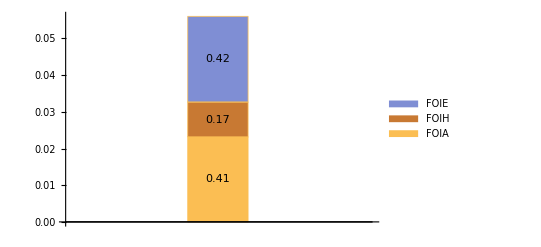
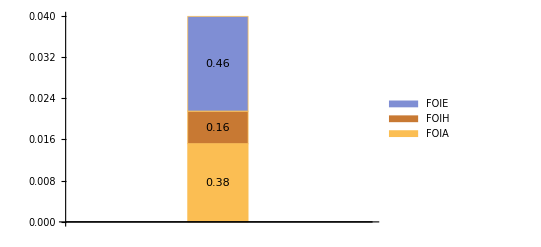
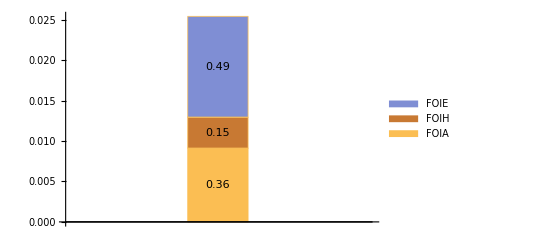

```mathematica
, ImageSize->Sum[FOITab[[n,x]],{x,3}]*2000
```

```mathematica
(*Get equilibrium values for different bAE*)
bAEvals = {0.001, 0.5, 0.9}
xyw = Table[Table[boundsol2[0.1, 1/100, 1/100, 1/100, p1][[1,n,2]], {n, 3}], {p1,bAEvals }];
xywU =Table[Table[unboundsol2[0.1, 1/100, 1/100, 1/100, p1][[1,n,2]], {n, 3}], {p1, bAEvals }];
(*Get forces of infection*)
FOITab = Table[{FOIA[xyw[[row, 1]], xyw[[row, 2]], 1/100], FOIE[xyw[[row, 1]], xyw[[row, 3]],bAEvals [[row]]], FOIH[xyw[[row,1]], 1/10]}, {row, 3}] ;
FOITabU = Table[{FOIA[xywU[[row, 1]], xywU[[row, 2]], 1/100], FOIE[xywU[[row, 1]], xywU[[row, 3]],bAEvals [[row]]], FOIH[xywU[[row,1]], 1/10]}, {row, 3}] ;
ProportionsFOI = Table[Table[FOITab[[n,i]]/Sum[FOITab[[n,x]],{x,3}], {i,3}], {n,3}];
ProportionsFOIU = Table[Table[FOITabU[[n,i]]/Sum[FOITabU[[n,x]],{x,3}], {i,3}], {n,3}];
tottransmission=Round[Table[Sum[FOITab[[n,x]],{x,3}], {n,1,3}],0.001];
tottransmissionU=Round[Table[Sum[FOITabU[[n,x]],{x,3}], {n,1,3}],0.001];
plotlables = Table[("Tot. transmission = "<>ToString[tottransmission[[n]]]"β_AE = "<>ToString[bAEvals[[n]]]),{n,1,3}];
plotlablesU = Table[("Tot. transmission = "<>ToString[tottransmissionU[[n]]]"β_AE = "<>ToString[bAEvals[[n]]]),{n,1,3}];
```

{0.001,0.5,0.9}

```mathematica
Table[PieChart[FOITab[[n]], ChartLegends->{"FOIA","FOIE","FOIH"},ChartLabels->Round[ProportionsFOI[[n]], 0.01], PlotLabel->Pane[plotlables[[n]],70]], {n,1,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PieChart[FOITabU[[n]],  ChartLegends->{"FOIA","FOIE","FOIH"},ChartLabels->Round[ProportionsFOIU[[n]], 0.01], PlotLabel->Pane[plotlablesU[[n]],70]], {n,1,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

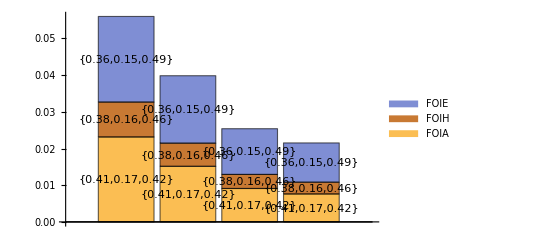

```mathematica
BarChart[FOITab, ChartLayout-> "Stacked", ChartLegends -> {"FOIA", "FOIH", "FOIE"}, ChartLabels -> Placed[Round[ProportionsFOI, 0.01], Center]]
```

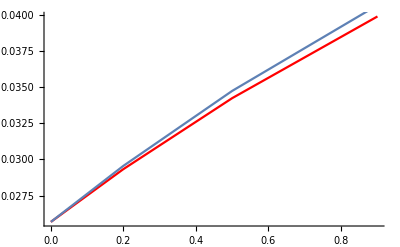

```mathematica
Show[ListLinePlot[Transpose[{bEHvals, Table[Sum[FOITab[[n,x]],{x,3}], {n,1,4}]}], PlotStyle->Red],ListLinePlot[Transpose[{bEHvals, Table[Sum[FOITabU[[n,x]],{x,3}], {n,1,4}]}]]]
```

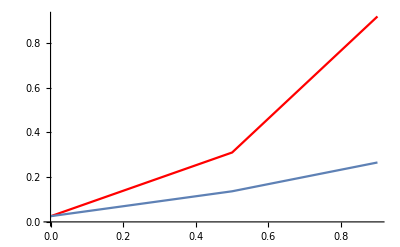

```mathematica
Show[ListLinePlot[Transpose[{bAEvals, Table[Sum[FOITabU[[n,x]],{x,3}], {n,1,3}]}], PlotStyle->Red],ListLinePlot[Transpose[{bAEvals, Table[Sum[FOITab[[n,x]],{x,3}], {n,1,3}]}]]]
```

```mathematica
impact[RH_, RCH_] := 1 - (RCH/RH)
```

```mathematica
(* environment dominated - LA usually 0.1, bEH, bHE, bEA, bAE usually 0.14 (U) or 0.23 (B) *)
scen1U[LA_, bEH_, bHE_,bEA_,bAE_] :=Evaluate[NSolve[{Unbounded[[1]]==0, Unbounded[[2]]==0, Unbounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, AH]->1/1000,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t]}, Reals]][[1,1,2]]
scen1B[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Bounded[[1]]==0, Bounded[[2]]==0, Bounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, AH]->1/1000,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t]}, Reals]][[1,1,2]]
(* animal dominated - LA usually 0.1, bEH usually 0.001, bEA usually 0.001, bHE 0.001, bAE usually 0.2 *)
scen2U[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Unbounded[[1]]==0, Unbounded[[2]]==0, Unbounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 0.2,Subscript[β, AH]->0.2,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t]}, Reals]][[1,1,2]]
scen2B[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Bounded[[1]]==0, Bounded[[2]]==0, Bounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 0.2,Subscript[β, AH]->0.2,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t]}, Reals]][[1,1,2]]
(*base values - relatively balanced - LA usually 0.1, bEH usually 0.01, bHE usually 1/10, bEA usually 0.01, bAE usually 0.1*)
baseU[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Unbounded[[1]]==0, Unbounded[[2]]==0, Unbounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> bEH, Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000},{x[t], y[t], w[t]}, Reals]][[1,1,2]]
baseB[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Bounded[[1]]==0, Bounded[[2]]==0, Bounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> bEH, Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000},{x[t], y[t], w[t]}, Reals]][[1,1,2]]
(* human dominated - LA usually 0.1, bEH usually 0.001, bEA usually 0.001, bHE 0.2, bAE usually 0.001 *)
scen3U[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Unbounded[[1]]==0, Unbounded[[2]]==0, Unbounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]->0.2, Subscript[β, AA]-> 1/1000,Subscript[β, AH]->1/1000,Subscript[β, HA]->0.2, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t]}, Reals]][[1,1,2]]
scen3B[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Bounded[[1]]==0, Bounded[[2]]==0, Bounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.
{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 0.2, Subscript[β, AA]-> 1/1000,Subscript[β, AH]->1/1000,Subscript[β, HA]->0.2, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t]}, Reals]][[1,1,2]]
```

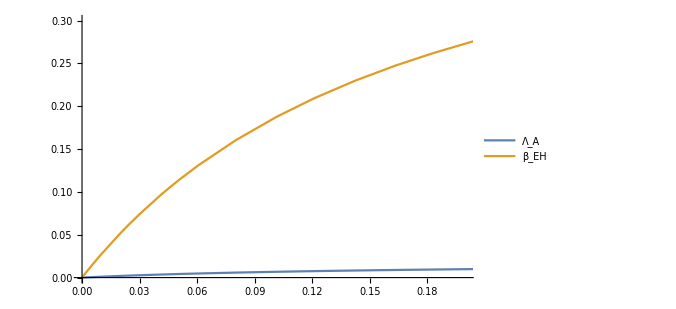
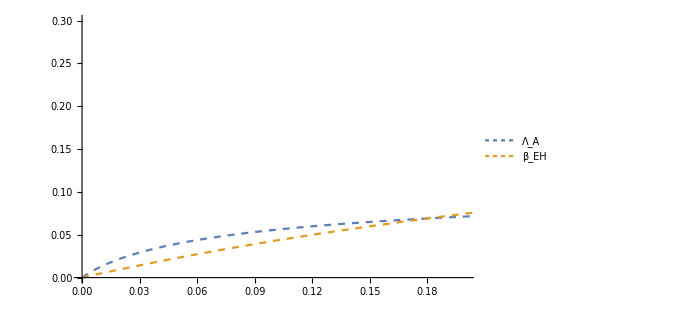
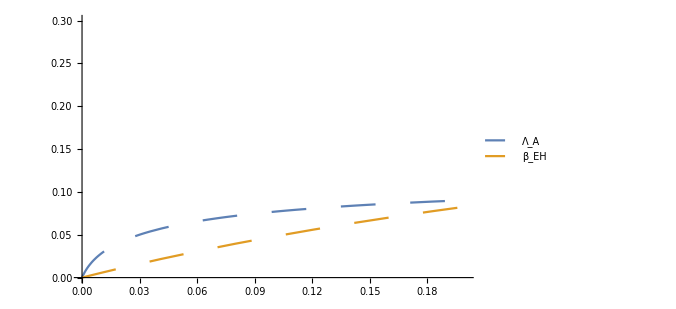
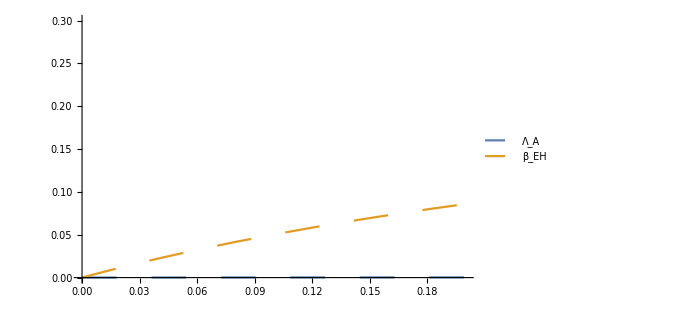
Row[-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
(*plot impact of reducing either LA or BEH to 0*)
b1impact = Plot[
{impact[scen1B[par1, 0.23, 0.23, 0.23, 0.23],scen1B[0., 0.23, 0.23, 0.23, 0.23]],
impact[scen1B[0.1, par1,  0.23, 0.23, 0.23], scen1B[0.1, 0.,  0.23, 0.23, 0.23]]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotRange -> {{0,0.2},{0, 0.3}}, PlotStyle -> Thick, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold, Font->32], ImageSize->500, TicksStyle->Large];
b2impact = Plot[
{impact[scen2B[par1, 0.001, 0.001, 0.001, 0.2],scen2B[0.,  0.001, 0.001, 0.001, 0.2]],
impact[scen2B[0.1, par1, 0.001, 0.001, 0.2],scen2B[0.1, 0.,  0.001, 0.001, 0.2] ]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.01], Thick}, {Dashing[0.01], Thick}}, PlotRange -> {{0,0.2},{0, 0.3}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold, Font->32],  ImageSize->500, TicksStyle->Large];
b3impact = Plot[
{impact[baseB[par1,0.01, 0.1, 0.01, 0.1],baseB[0., 0.01, 0.1, 0.01, 0.1]],
impact[baseB[0.1, par1, 0.1, 0.01, 0.1],baseB[0.1, 0., 0.1, 0.01, 0.1]]} ,
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.05], Thick}}, PlotRange -> {{0,0.2},{0, 0.3}}, LabelStyle->Directive[Bold, Large], AxesStyle->Directive[Bold, Font->32], ImageSize->500, TicksStyle->Large];
b4impact = Plot[
{impact[scen3B[par1,0.001, 0.2, 0.001, 0.001],scen3B[0., 0.001, 0.2, 0.001, 0.001]],
impact[scen3B[0.1, par1, 0.2, 0.001, 0.001],scen3B[0.1, 0., 0.2, 0.001, 0.001]]} ,
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.05], Thick}}, PlotRange -> {{0,0.2},{0, 0.3}}, LabelStyle->Directive[Bold, Large], AxesStyle->Directive[Bold, Font->32], ImageSize->500, TicksStyle->Large];
Row[b1impact,b2impact,b3impact, b4impact]
```

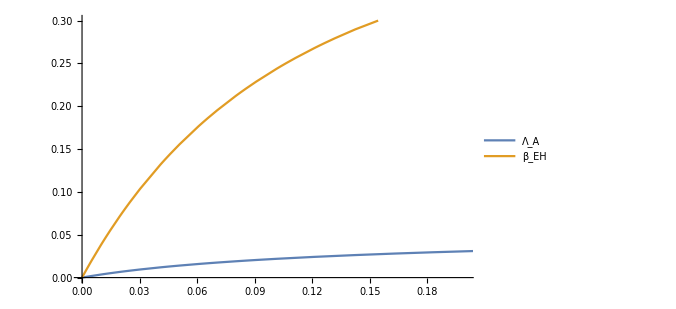
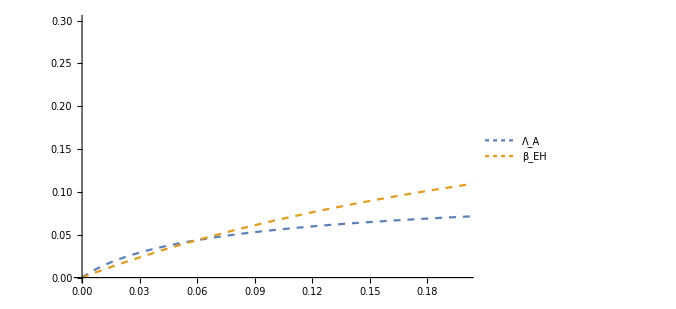
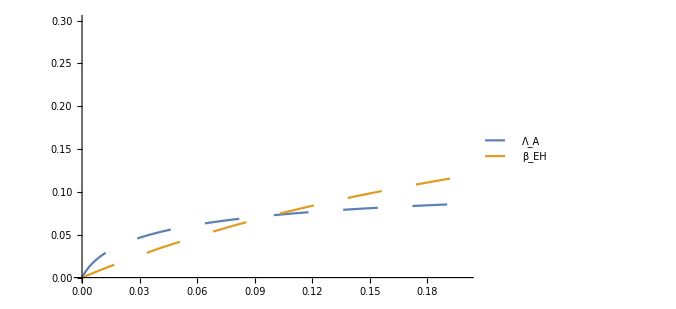
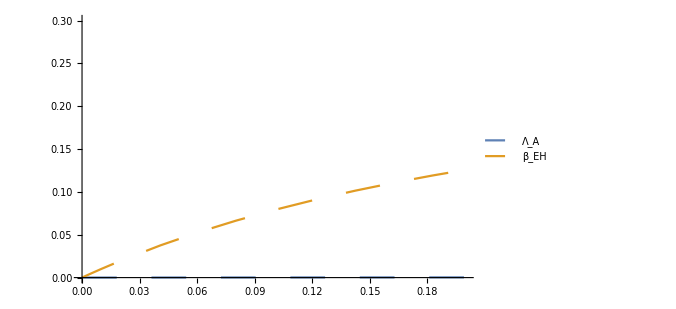
Row[-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
u1impact = Plot[
{impact[scen1U[par1, 0.14, 0.14,  0.14, 0.14],scen1U[0.,  0.14,  0.14,  0.14, 0.14]],
impact[scen1U[0.1, par1,   0.14,  0.14, 0.14], scen1U[0.1, 0.,   0.14,  0.14, 0.14]]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotRange -> {{0,0.2},{0, 0.3}}, PlotStyle -> Thick, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold],  ImageSize->500, TicksStyle->Large];
u2impact = Plot[
{impact[scen2U[par1,0.001, 0.001, 0.001, 0.2],scen2U[0., 0.001, 0.001, 0.001, 0.2]],
impact[scen2U[0.1, par1, 0.001, 0.001, 0.2],scen2U[0.1, 0.,  0.001, 0.001, 0.2] ]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.01], Thick}, {Dashing[0.01], Thick}}, PlotRange -> {{0,0.2},{0, 0.3}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold], ImageSize->500, TicksStyle->Large];
u3impact = Plot[
{impact[baseU[par1,0.01, 0.1, 0.01, 0.1],baseU[0., 0.01, 0.1, 0.01, 0.1]],
impact[baseU[0.1, par1, 0.1, 0.01, 0.1],baseU[0.1, 0., 0.1, 0.01, 0.1]]} ,
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.05], Thick}}, PlotRange -> {{0,0.2},{0, 0.3}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold], ImageSize->500, TicksStyle->Large];
u4impact = Plot[
{impact[scen3U[par1,0.001, 0.2, 0.001, 0.001],scen3U[0., 0.001, 0.2, 0.001, 0.001]],
impact[scen3U[0.1, par1, 0.2, 0.001, 0.001],scen3U[0.1, 0., 0.2, 0.001, 0.001]]} ,
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.05], Thick}}, PlotRange -> {{0,0.2},{0, 0.3}}, LabelStyle->Directive[Bold, Large], AxesStyle->Directive[Bold, Font->32], ImageSize->500, TicksStyle->Large];
Row[u1impact,u2impact,u3impact, u4impact]
```

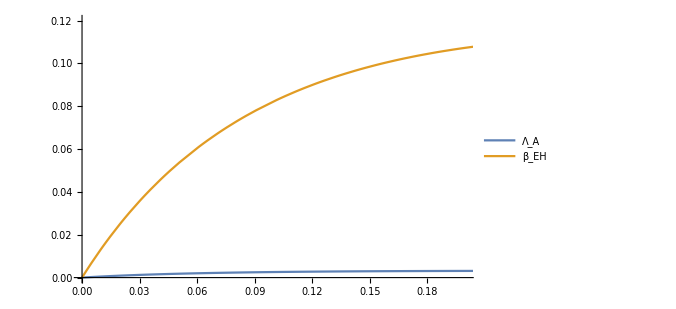
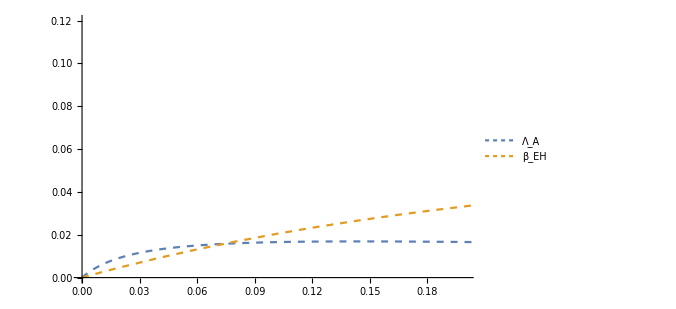
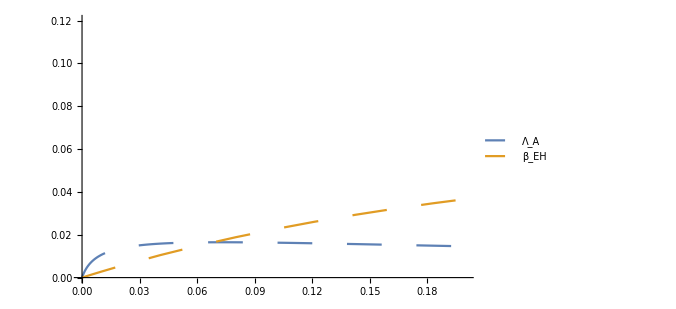
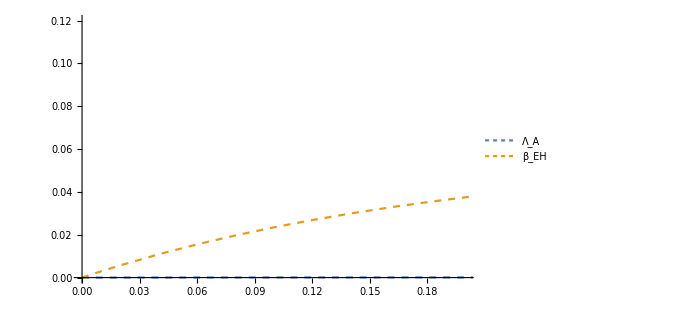
Row[-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
(*plot impact of reducing either LA or BEH by 0.5*)
b1impact = Plot[
{impact[scen1B[par1, 0.23, 0.23, 0.23, 0.23],scen1B[par1*0.5, 0.23, 0.23, 0.23, 0.23]],
impact[scen1B[0.1, par1,  0.23, 0.23, 0.23], scen1B[0.1,par1*0.5,  0.23, 0.23, 0.23]]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotRange -> {{0,0.2},{0, 0.12}}, PlotStyle -> Thick, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold], ImageSize->500, TicksStyle->Large];
b2impact = Plot[
{impact[scen2B[par1, 0.001, 0.001, 0.001, 0.2],scen2B[par1*0.5,  0.001, 0.001, 0.001, 0.2]],
impact[scen2B[0.1, par1, 0.001, 0.001, 0.2],scen2B[0.1, par1*0.5,  0.001, 0.001, 0.2] ]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.01], Thick}, {Dashing[0.01], Thick}}, PlotRange -> {{0,0.2},{0, 0.12}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold], ImageSize->500, TicksStyle->Large];
b3impact = Plot[
{impact[baseB[par1,0.01, 0.1, 0.01, 0.1],baseB[par1*0.5, 0.01, 0.1, 0.01, 0.1]],
impact[baseB[0.1, par1, 0.1, 0.01, 0.1],baseB[0.1, par1*0.5, 0.1, 0.01, 0.1]]} ,
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.05], Thick}}, PlotRange -> {{0,0.2},{0, 0.12}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold], ImageSize->500, TicksStyle->Large];
b4impact = Plot[
{impact[scen3B[par1,0.001, 0.2, 0.001, 0.001],scen3B[par1*0.5, 0.001, 0.2, 0.001, 0.001]],
impact[scen3B[0.1, par1, 0.2, 0.001, 0.001],scen3B[0.1, par1*0.5,  0.2, 0.001, 0.001] ]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.01], Thick}, {Dashing[0.01], Thick}}, PlotRange -> {{0,0.2},{0, 0.12}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold], ImageSize->500, TicksStyle->Large];
Row[b1impact,b2impact,b3impact, b4impact]
```

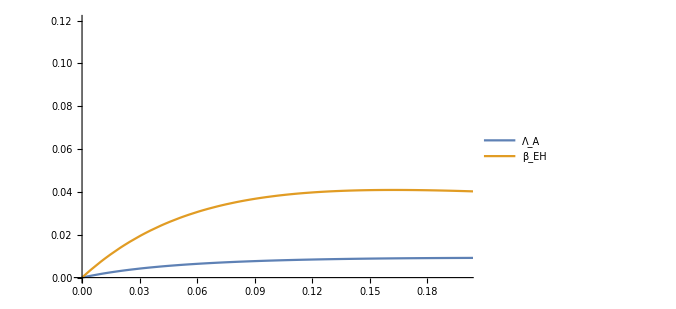
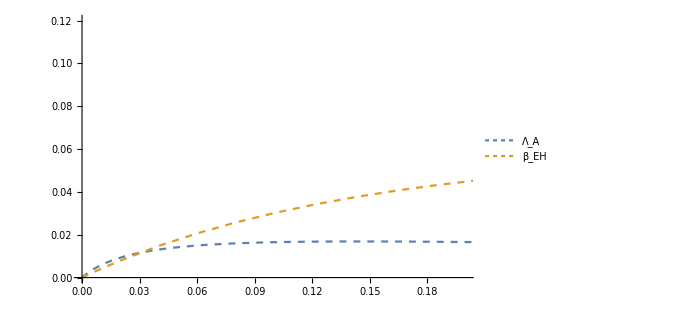
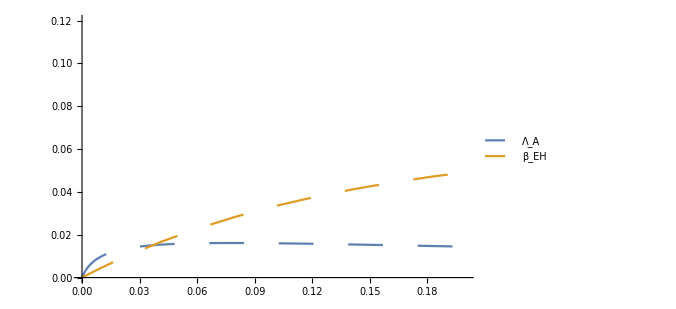
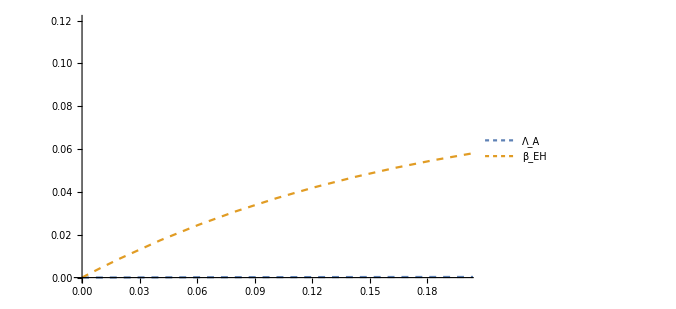
Row[-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
u1impact = Plot[
{impact[scen1U[par1, 0.14, 0.14,  0.14, 0.14],scen1U[par1*0.5,  0.14,  0.14,  0.14, 0.14]],
impact[scen1U[0.1, par1,   0.14,  0.14, 0.14], scen1U[0.1, par1*0.8,   0.14,  0.14, 0.14]]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotRange -> {{0,0.2},{0, 0.12}}, PlotStyle -> Thick, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold],  ImageSize->500, TicksStyle->Large];
u2impact = Plot[
{impact[scen2U[par1,0.001, 0.001, 0.001, 0.2],scen2U[par1*0.5, 0.001, 0.001, 0.001, 0.2]],
impact[scen2U[0.1, par1, 0.001, 0.001, 0.2],scen2U[0.1,par1*0.5,  0.001, 0.001, 0.2] ]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.01], Thick}, {Dashing[0.01], Thick}}, PlotRange -> {{0,0.2},{0, 0.12}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold],  ImageSize->500, TicksStyle->Large];
u3impact = Plot[
{impact[baseU[par1,0.01, 0.1, 0.01, 0.1],baseU[par1*0.5, 0.01, 0.1, 0.01, 0.1]],
impact[baseU[0.1, par1, 0.1, 0.01, 0.1],baseU[0.1, par1*0.5, 0.1, 0.01, 0.1]]} ,
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.05], Thick}}, PlotRange -> {{0,0.2},{0, 0.12}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold],  ImageSize->500, TicksStyle->Large];
u4impact = Plot[
{impact[scen3U[par1, 0.001, 0.2, 0.001, 0.001],scen3U[par1*0.5, 0.001, 0.2, 0.001, 0.001]],
impact[scen3U[0.1, par1, 0.2, 0.001, 0.001],scen3U[0.1, par1*0.5,  0.2, 0.001, 0.001] ]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A","β_EH"}, PlotStyle->{{Dashing[0.01], Thick}, {Dashing[0.01], Thick}}, PlotRange -> {{0,0.2},{0, 0.12}}, LabelStyle->Directive[Bold], AxesStyle->Directive[Bold], ImageSize->500, TicksStyle->Large];
Row[u1impact,u2impact,u3impact, u4impact]
```

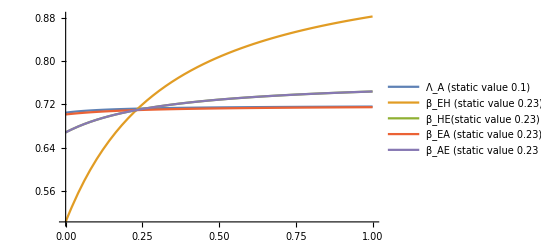
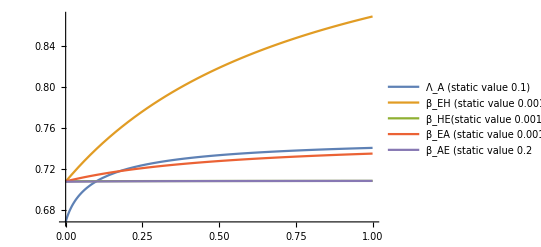
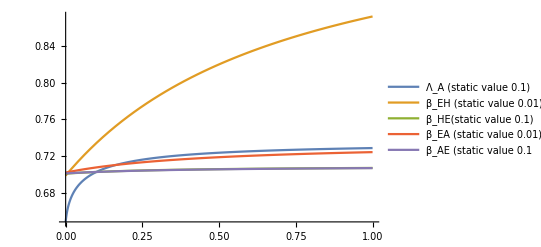
Row[-Graphics-,-Graphics-,-Graphics-]

```mathematica
b1 = Plot[
{scen1B[par1, 0.23, 0.23, 0.23, 0.23],
scen1B[1/10, par1, 0.23, 0.23, 0.23], 
scen1B[1/10, 0.23, par1, 0.23, 0.23], 
scen1B[1/10, 0.23, 0.23,par1, 0.23], 
scen1B[1/10, 0.23, 0.23, 0.23, par1]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A (static value 0.1)","β_EH (static value 0.23)", "β_HE(static value 0.23)","β_EA (static value 0.23)", "β_AE (static value 0.23"}, PlotRange->All];
b2 = Plot[
{scen2B[par1,0.001, 0.001, 0.001, 0.2],
scen2B[0.1,par1, 0.001, 0.001, 0.2], 
scen2B[0.1,0.001, par1, 0.001, 0.2],
scen2B[0.1,0.001, 0.001, par1, 0.2],
scen2B[0.1,0.001, 0.001, 0.001,par1]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A (static value 0.1)","β_EH (static value 0.001)", "β_HE(static value 0.001)","β_EA (static value 0.001)", "β_AE (static value 0.2"}, PlotRange->All];
b3 = Plot[
{baseB[par1, 1/100, 1/10, 1/100, 1/10],
baseB[1/10, par1, 1/10, 1/100, 1/10], 
baseB[1/10, 1/100, par1, 1/100, 1/10], 
baseB[1/10, 1/100, 1/10,par1, 1/10], 
baseB[1/10, 1/100, 1/10, 1/100, par1]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A (static value 0.1)","β_EH (static value 0.01)", "β_HE(static value 0.1)","β_EA (static value 0.01)", "β_AE (static value 0.1"}, PlotRange->All];
Row[b1, b2, b3]
```

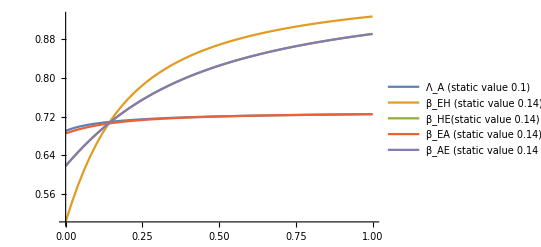
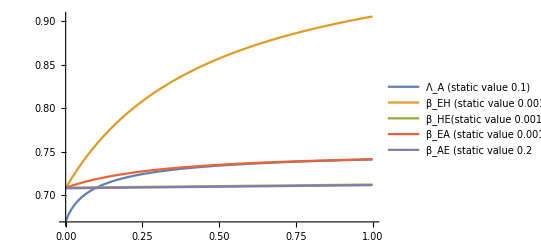
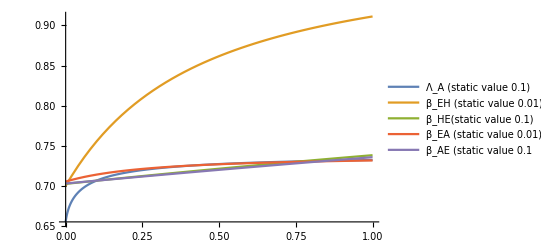
Row[-Graphics-,-Graphics-,-Graphics-]

```mathematica
u1 = Plot[
{scen1U[par1, 0.14, 0.14, 0.14, 0.14],
scen1U[1/10, par1, 0.14, 0.14, 0.14], 
scen1U[1/10, 0.14, par1, 0.14, 0.14], 
scen1U[1/10, 0.14, 0.14,par1, 0.14], 
scen1U[1/10, 0.14, 0.14, 0.14, par1]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A (static value 0.1)","β_EH (static value 0.14)", "β_HE(static value 0.14)","β_EA (static value 0.14)", "β_AE (static value 0.14"}, PlotRange->All];
u2 = Plot[
{scen2U[par1,0.001, 0.001, 0.001, 0.2],
scen2U[0.1,par1, 0.001, 0.001, 0.2], 
scen2U[0.1,0.001, par1, 0.001, 0.2],
scen2U[0.1,0.001, 0.001, par1, 0.2],
scen2U[0.1,0.001, 0.001, 0.001,par1]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A (static value 0.1)","β_EH (static value 0.001)", "β_HE(static value 0.001)","β_EA (static value 0.001)", "β_AE (static value 0.2"}, PlotRange->All];
u3 = Plot[
{baseU[par1, 1/100, 1/10, 1/100, 1/10],
baseU[1/10, par1, 1/10, 1/100, 1/10], 
baseU[1/10, 1/100, par1, 1/100, 1/10], 
baseU[1/10, 1/100, 1/10,par1, 1/10], 
baseU[1/10, 1/100, 1/10, 1/100, par1]},
{par1, 0., 1.},
PlotLegends-> {"Λ_A (static value 0.1)","β_EH (static value 0.01)", "β_HE(static value 0.1)","β_EA (static value 0.01)", "β_AE (static value 0.1"}, PlotRange->All];
Row[u1, u2, u3]
```

```mathematica
(*contour plots to show how impact of LA changes over betaEH*)
scen1Bcontourplot = ContourPlot[
impact[scen1B[par2, par1, 0.23,  0.23, 0.23],scen1B[0.,  par1,  0.23,  0.23, 0.23]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All, ImageSize->500, FrameTicksStyle->Large];
scen1Ucontourplot = ContourPlot[
impact[scen1U[par2, par1, 0.14,  0.14, 0.14],scen1U[0.,  par1,  0.14,  0.14, 0.14]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All,  ImageSize->500, FrameTicksStyle->Large];
```

```mathematica
scen2Bcontourplot = ContourPlot[
impact[scen2B[par2, par1, 0.001, 0.001, 0.2],scen2B[0.,  par1, 0.001, 0.001, 0.2]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All, ImageSize->500, FrameTicksStyle->Large];
scen2Ucontourplot = ContourPlot[
impact[scen2U[par2, par1, 0.001, 0.001, 0.2],scen2U[0.,  par1, 0.001, 0.001, 0.2]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All, ImageSize->500, FrameTicksStyle->Large];
```

```mathematica
baseBcontourplot = ContourPlot[
impact[baseU[par2,par1, 0.1, 0.01, 0.1],baseU[0., par1, 0.1, 0.01, 0.1]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All,  ImageSize->500, FrameTicksStyle->Large];
baseUcontourplot = ContourPlot[
impact[baseU[par2,par1, 0.1, 0.01, 0.1],baseU[0., par1, 0.1, 0.01, 0.1]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All, ImageSize->500, FrameTicksStyle->Large];
```

```mathematica
scen3Bcontourplot = ContourPlot[
impact[scen3B[par2, par1, 0.2, 0.001, 0.001],scen3B[0.,  par1, 0.2, 0.001, 0.001]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All, ImageSize->500, FrameTicksStyle->Large];
scen3Ucontourplot = ContourPlot[
impact[scen3U[par2, par1, 0.2, 0.001, 0.001],scen3U[0.,  par1, 0.2, 0.001, 0.001]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.1}}], PlotRange -> All, ImageSize->500, FrameTicksStyle->Large];
```

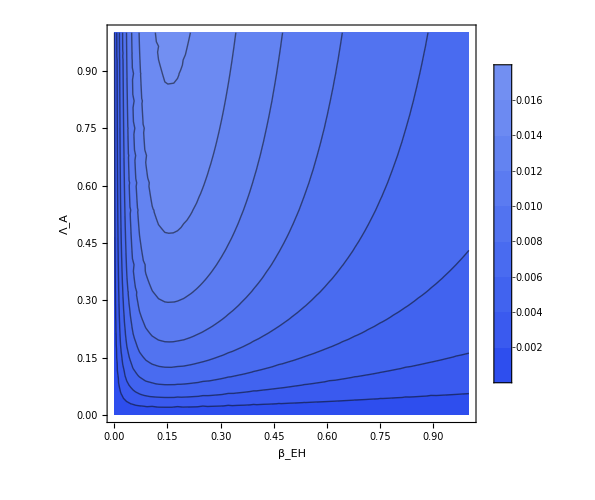
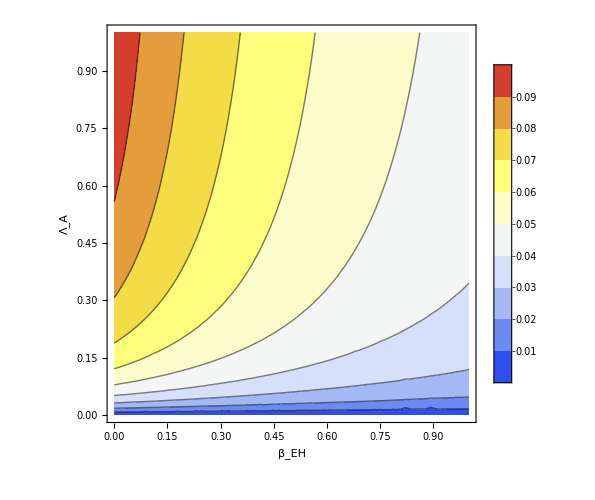
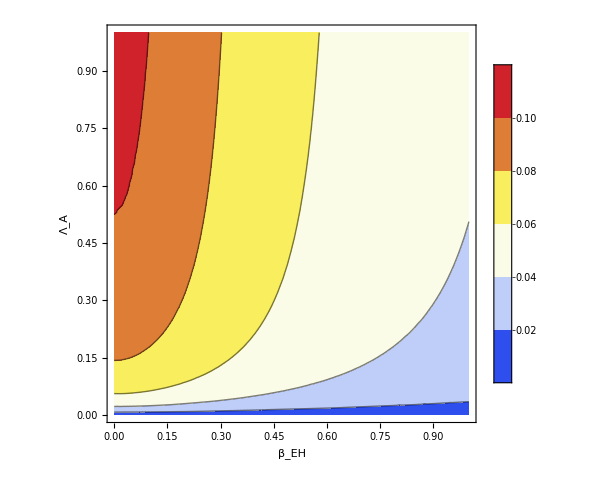
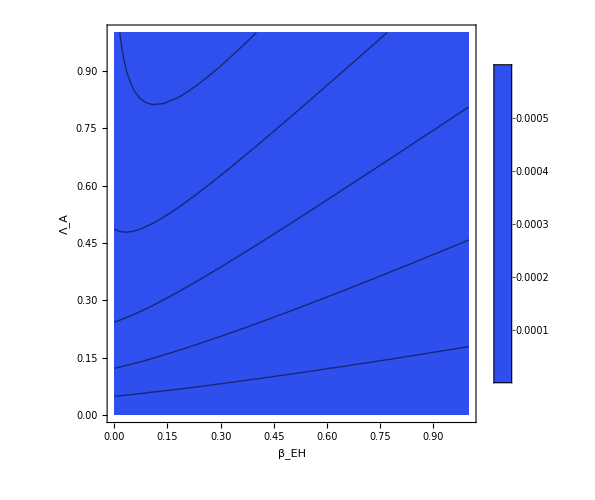
Row[-Graphics-,-Graphics-,-Graphics-,-Graphics-]

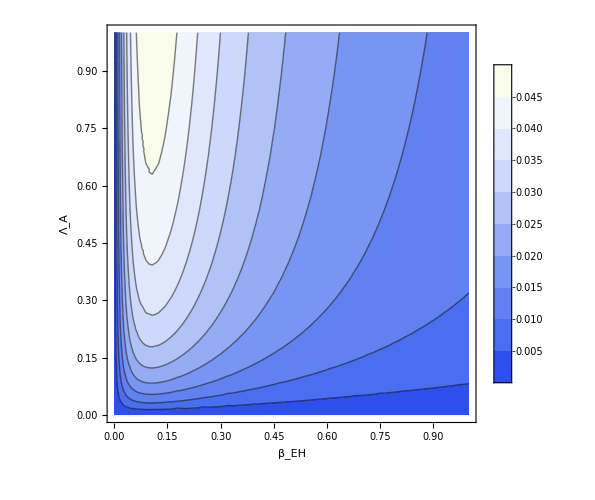
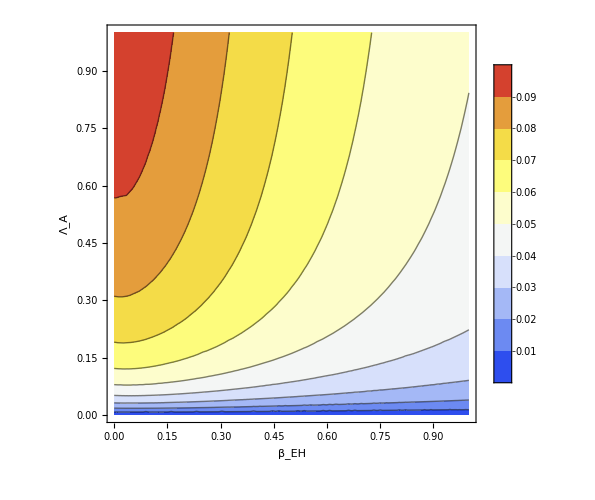
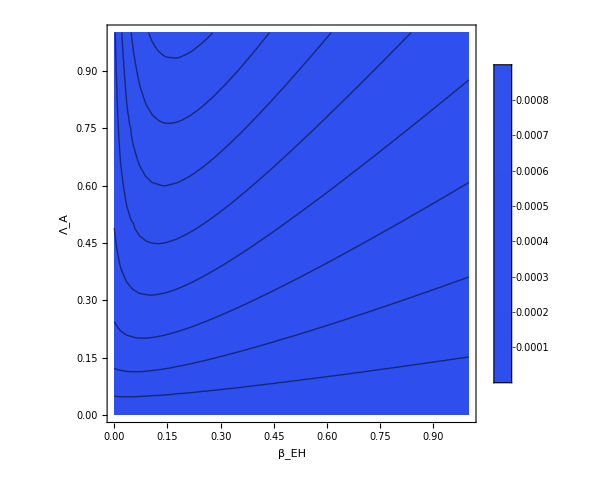
Row[-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
Row[scen1Bcontourplot, scen2Bcontourplot, baseBcontourplot, scen3Bcontourplot]
Row[scen1Ucontourplot, scen2Ucontourplot, baseUcontourplot, scen3Ucontourplot]
```

```mathematica
(* environment dominated - LA usually 0.1, bEH, bHE, bEA, bAE usually 0.14 (U) or 0.23 (B) *)
scen1UREA[LA_, bEH_, bHE_,bEA_,bAE_] :=Evaluate[NSolve[{Unboundfrac[[1]]==0, Unboundfrac[[2]]==0, Unboundfrac[[3]]==0, Unboundfrac[[4]]==0, Unboundfrac[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t]≥ 0 && r[t]≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, AH]->1/1000,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t], z[t], r[t]}, Reals]][[1,5,2]]
scen1BREA[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Boundfrac[[1]]==0, Boundfrac[[2]]==0, Boundfrac[[3]]==0, Boundfrac[[4]]==0, Boundfrac[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t]≥ 0 && r[t]≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, AH]->1/1000,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t], z[t], r[t]}, Reals]][[1,5,2]]
(* animal dominated - LA usually 0.1, bEH usually 0.001, bEA usually 0.001, bHE 0.001, bAE usually 0.2 *)
scen2UREA[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Unboundfrac[[1]]==0, Unboundfrac[[2]]==0, Unboundfrac[[3]]==0, Unboundfrac[[4]]==0, Unboundfrac[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t]≥ 0 && r[t]≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 0.2,Subscript[β, AH]->0.2,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t], z[t], r[t]}, Reals]][[1,5,2]]
scen2BREA[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Boundfrac[[1]]==0, Boundfrac[[2]]==0, Boundfrac[[3]]==0, Boundfrac[[4]]==0, Boundfrac[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t]≥ 0 && r[t]≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 0.2,Subscript[β, AH]->0.2,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t], z[t], r[t]}, Reals]][[1,5,2]]
(*base values - relatively balanced - LA usually 0.1, bEH usually 0.01, bHE usually 1/10, bEA usually 0.01, bAE usually 0.1*)
baseUREA[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Unboundfrac[[1]]==0, Unboundfrac[[2]]==0, Unboundfrac[[3]]==0, Unboundfrac[[4]]==0, Unboundfrac[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t]≥ 0 && r[t]≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> bEH, Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000},{x[t], y[t], w[t], z[t], r[t]}, Reals]][[1,5,2]]
baseBREA[LA_, bEH_, bHE_,bEA_,bAE_] :=
Evaluate[NSolve[{Boundfrac[[1]]==0, Boundfrac[[2]]==0, Boundfrac[[3]]==0, Boundfrac[[4]]==0, Boundfrac[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t]≥ 0 && r[t]≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> bEH, Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000},{x[t], y[t], w[t], z[t], r[t]}, Reals]][[1,5,2]]
```

```mathematica
CPUREAs1 = ContourPlot[scen1UREA[y, 0.14, 0.14, 0.14, x],{x,0.,0.2},{y,0.,1.}, PlotLegends->Automatic, FrameLabel->{Style["β_AE", 32],Style["Λ_A",32]},  LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 1.}}], ImageSize->500, FrameTicksStyle->Large];
CPBREAs1  = ContourPlot[scen1BREA[y, 0.23, 0.23, 0.23, x],{x,0.,0.2},{y,0.,1.}, PlotLegends->Automatic, FrameLabel->{Style["β_AE", 32],Style["Λ_A",32]}, LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 1.}}], ImageSize->500, FrameTicksStyle->Large];

CPUREAs2 = ContourPlot[scen2UREA[y, 1/1000, 1/1000, 1/1000, x],{x,0.,0.2},{y,0.,1.}, PlotLegends->Automatic, FrameLabel->{Style["β_AE", 32],Style["Λ_A",32]},  LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 1.}}], ImageSize->500, FrameTicksStyle->Large];
CPBREAs2  = ContourPlot[scen2BREA[y, 1/1000, 1/1000, 1/1000, x],{x,0.,0.2},{y,0.,1.}, PlotLegends->Automatic, FrameLabel->{Style["β_AE", 32],Style["Λ_A",32]}, LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 1.}}], ImageSize->500, FrameTicksStyle->Large];

CPUREA = ContourPlot[baseUREA[y, 1/100, 1/10, 1/100, x],{x,0.,0.2},{y,0.,1.}, PlotLegends->Automatic, FrameLabel->{Style["β_AE", 32],Style["Λ_A",32]},  LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 1.}}], ImageSize->500, FrameTicksStyle->Large];
CPBREA  = ContourPlot[baseBREA[y, 1/100, 1/10, 1/100, x],{x,0.,0.2},{y,0.,1.}, PlotLegends->Automatic, FrameLabel->{Style["β_AE", 32],Style["Λ_A",32]}, LabelStyle->Directive[Bold, Large], ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 1.}}], ImageSize->500, FrameTicksStyle->Large];
```

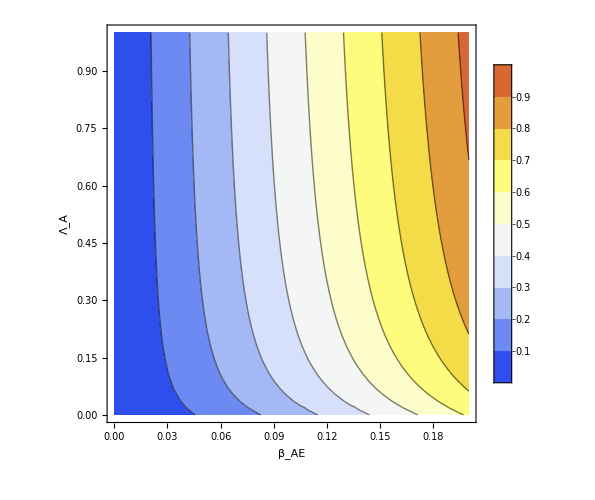
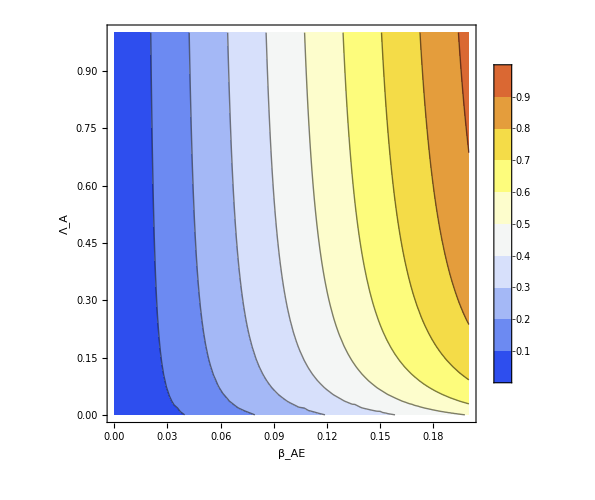
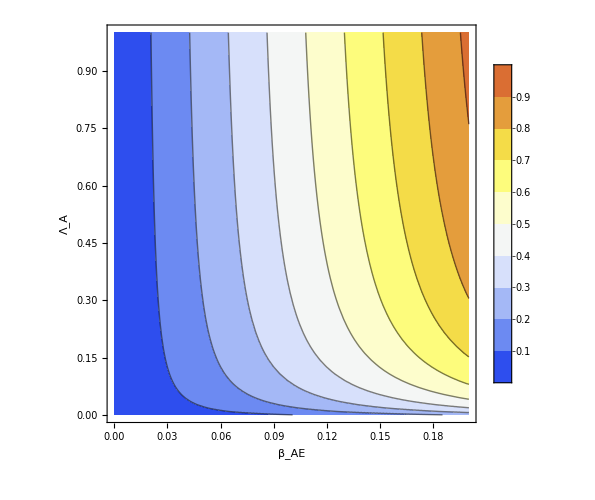
Row[-Graphics-,-Graphics-,-Graphics-]

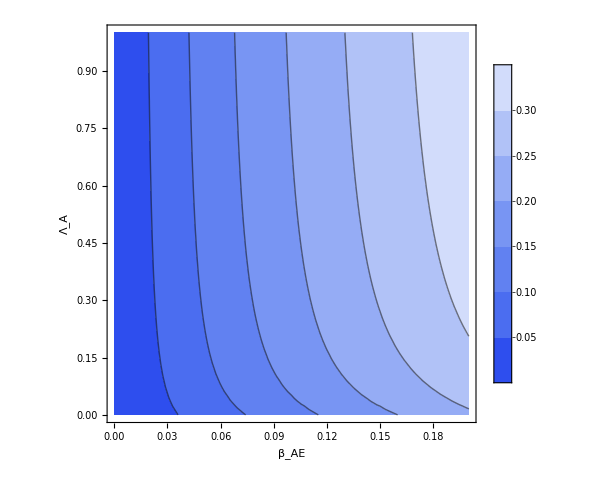
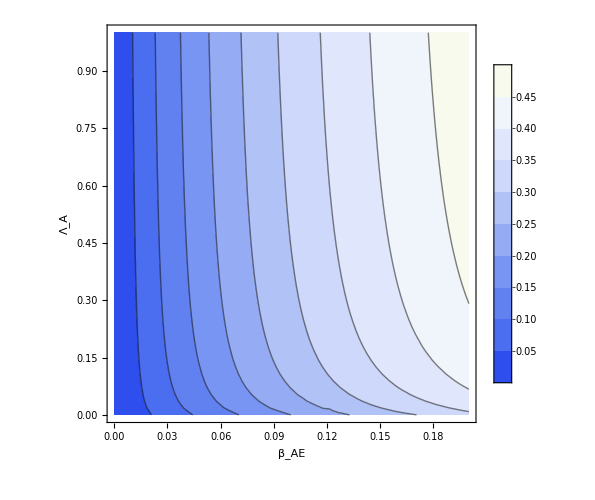
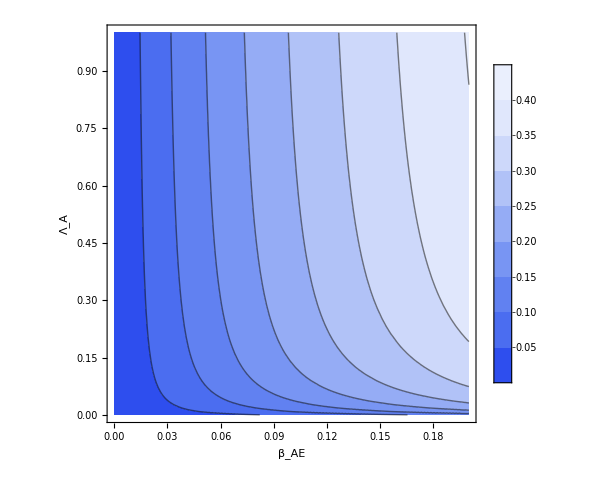
Row[-Graphics-,-Graphics-,-Graphics-]

```mathematica
Row[CPUREAs1, CPUREAs2, CPUREA]
Row[CPBREAs1, CPBREAs2, CPBREA]
```

```mathematica
(*Trajectory plots of all three transmission scenarios*)
```

```mathematica
solBB = NDSolve[{DiffBoundfrac/.
{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
tBB = Plot[{Evaluate[x[t]/.solBB[[1,1]]], Evaluate[y[t]/.solBB[[1,2]]], Evaluate[w[t]/.solBB[[1,3]]], Evaluate[z[t]/.solBB[[1,4]]], Evaluate[r[t]/.solBB[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large], ImageSize->500];
solUB = NDSolve[{DiffUnboundfrac/.
{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
tUB = Plot[{Evaluate[x[t]/.solUB[[1,1]]], Evaluate[y[t]/.solUB[[1,2]]], Evaluate[w[t]/.solUB[[1,3]]], Evaluate[z[t]/.solUB[[1,4]]], Evaluate[r[t]/.solUB[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],ImageSize->500];

sol1B = NDSolve[{DiffBoundfrac/.
{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/1000,Subscript[β, HH]->1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, EH] ->0.23, Subscript[β, EA]-> 0.23, Subscript[β, HE] -> 0.23, Subscript[β, AE] -> 0.23, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
t1B = Plot[{Evaluate[x[t]/.sol1B[[1,1]]], Evaluate[y[t]/.sol1B[[1,2]]], Evaluate[w[t]/.sol1B[[1,3]]], Evaluate[z[t]/.sol1B[[1,4]]], Evaluate[r[t]/.sol1B[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],ImageSize->500];
sol1U = NDSolve[{DiffUnboundfrac/.
{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/1000,Subscript[β, HH]->1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, EH] ->0.14, Subscript[β, EA]-> 0.14, Subscript[β, HE] -> 0.14, Subscript[β, AE] -> 0.14, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
t1U = Plot[{Evaluate[x[t]/.sol1U[[1,1]]], Evaluate[y[t]/.sol1U[[1,2]]], Evaluate[w[t]/.sol1U[[1,3]]], Evaluate[z[t]/.sol1U[[1,4]]], Evaluate[r[t]/.sol1U[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],ImageSize->500];

sol2B = NDSolve[{DiffBoundfrac/.
{Subscript[β, HA]->1/1000,Subscript[β, AH]->0.2,Subscript[β, HH]->1/1000, Subscript[β, AA]-> 0.2,Subscript[β, EH] ->1/1000, Subscript[β, EA]-> 1/1000, Subscript[β, HE] -> 1/1000, Subscript[β, AE] -> 0.2, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
t2B = Plot[{Evaluate[x[t]/.sol2B[[1,1]]], Evaluate[y[t]/.sol2B[[1,2]]], Evaluate[w[t]/.sol2B[[1,3]]], Evaluate[z[t]/.sol2B[[1,4]]], Evaluate[r[t]/.sol2B[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],ImageSize->500];
sol2U = NDSolve[{DiffUnboundfrac/.
{Subscript[β, HA]->1/1000,Subscript[β, AH]->0.2,Subscript[β, HH]->1/1000, Subscript[β, AA]-> 0.2,Subscript[β, EH] ->1/1000, Subscript[β, EA]-> 1/1000, Subscript[β, HE] -> 1/1000, Subscript[β, AE] -> 0.2, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
t2U = Plot[{Evaluate[x[t]/.sol2U[[1,1]]], Evaluate[y[t]/.sol2U[[1,2]]], Evaluate[w[t]/.sol2U[[1,3]]], Evaluate[z[t]/.sol2U[[1,4]]], Evaluate[r[t]/.sol2U[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],ImageSize->500];

sol3B = NDSolve[{DiffBoundfrac/.
{Subscript[β, HA]->0.14,Subscript[β, AH]->1/1000,Subscript[β, HH]->0.14, Subscript[β, AA]->1/1000,Subscript[β, EH] ->0.14, Subscript[β, EA]-> 1/1000, Subscript[β, HE] -> 0.14, Subscript[β, AE] ->1/1000, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
t3B = Plot[{Evaluate[x[t]/.sol3B[[1,1]]], Evaluate[y[t]/.sol3B[[1,2]]], Evaluate[w[t]/.sol3B[[1,3]]], Evaluate[z[t]/.sol3B[[1,4]]], Evaluate[r[t]/.sol3B[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],ImageSize->500];
sol3U = NDSolve[{DiffUnboundfrac/.
{Subscript[β, HA]->0.125,Subscript[β, AH]->1/1000,Subscript[β, HH]->0.125, Subscript[β, AA]->1/1000,Subscript[β, EH] ->0.125, Subscript[β, EA]-> 1/1000, Subscript[β, HE] -> 0.125, Subscript[β, AE] ->1/1000, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
t3U = Plot[{Evaluate[x[t]/.sol3U[[1,1]]], Evaluate[y[t]/.sol3U[[1,2]]], Evaluate[w[t]/.sol3U[[1,3]]], Evaluate[z[t]/.sol3U[[1,4]]], Evaluate[r[t]/.sol3U[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],ImageSize->500];
```

```mathematica
Row[t1B, t2B, tBB, t3B]
Row[t1U, t2U, tUB, t3U]
```

```mathematica
solBB = NDSolve[{DiffBoundfrac/.
{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/10, Subscript[β, EA]-> 1/10, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
tBB = Plot[{Evaluate[x[t]/.solBB[[1,1]]], Evaluate[y[t]/.solBB[[1,2]]], Evaluate[w[t]/.solBB[[1,3]]], Evaluate[z[t]/.solBB[[1,4]]], Evaluate[r[t]/.solBB[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large], ImageSize->500]
solUB = NDSolve[{DiffUnboundfrac/.
{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 1/10, Subscript[β, EA]-> 1/10, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, x[0] == 0, y[0]== 0, w[0]==0, z[0] == 0, r[0] == 0}, {x,y, w, z, r}, {t, 0, 1000}];
tUB = Plot[{Evaluate[x[t]/.solUB[[1,1]]], Evaluate[y[t]/.solUB[[1,2]]], Evaluate[w[t]/.solUB[[1,3]]], Evaluate[z[t]/.solUB[[1,4]]], Evaluate[r[t]/.solUB[[1,5]]]}, {t,0,1000}, PlotStyle -> {Dashing[0.01], Dashing[0.02], Dashing[0.03], Dashing[0.04], Dashing[0.05]}, PlotRange->{{0,500},{0.0,1.0}},PlotLegends->{"R_H", "R_A", "R_E", "R_E(H)", "R_E(A)"},PlotTheme->{"Detailed", "ThickLines"},PlotRange->All,  FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large],ImageSize->500]
```

```mathematica
(*Explain optimal impact area *)
unboundsol2[LA_, bEH_, bEA_, bHE_, bAE_] :=NSolve[{Unbounded[[1]]==0., Unbounded[[2]]==0., Unbounded[[3]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/100,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->bEH, Subscript[β, EA]-> bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->LA,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals];
FOIELAfrac[L_, A_, AE_] := L * AE * A
FOIEotherfrac[L_, AE_,HE_,A_,H_] := AE*A + HE*H
ratioLAOtherEnv[LA_, bHE_] := Module[{L = LA, HE = bHE},
sol1 = Table[unboundsol2[L, 0.14, 0.14, HE, 0.14][[1,n,2]], {n,1,3}];
FLA =FOIELAfrac[L, sol1[[2]], HE];
FO = FOIEotherfrac[L, 0.14, HE,sol1[[2]],sol1[[1]]];
FLA/FO
]
```

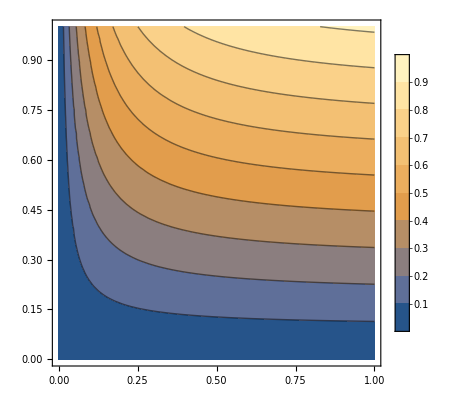

```mathematica
ContourPlot[ratioLAOtherEnv[LA, HE],  {HE, 0., 1.0}, {LA, 0., 1.0}, PlotLegends->Automatic]
```

```mathematica
(*this is wrong still*)
FOIHLAfrac[L_,AE_,EH_,AH_, A_,Env_,H_] := (1-H)L(1-A)(AH A +AE A EH Env)
FOIHOtherfrac[L_,EH_,AH_, A_,Env_,H_] := (1-L)(1-H)(AH A + EH Env)
ratioLAOtherH[LA_,bAE_,bEH_,bAH_]:=Module[{L= LA,AE =bAE, EH = bEH, AH = bAH},
sol1 = Table[unboundsol2[L, EH, 0.14, 0.14, 0.14][[1,n,2]], {n,1,3}];
FLA =FOIHLAfrac[L,AE,EH,AH, sol1[[2]],sol1[[3]],sol1[[1]]];
FO =FOIHOtherfrac[L,EH,AH, sol1[[2]],sol1[[3]],sol1[[1]]];
FLA/FO
]
ContourPlot[ratioLAOtherH[LA, 0.14, BEH, 0.001],  {BEH, 0., 1.0}, {LA, 0., 1.0}]
impact[R_, RI_] := 1 - RI/R
```

Part::partd: Part specification unboundsol2[0.0000714286,0.0000714286,0.14,0.14,0.14]⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification unboundsol2[0.0000714286,0.0000714286,0.14,0.14,0.14]⟦1,2,2⟧ is longer than depth of object.

Part::partd: Part specification unboundsol2[0.0000714286,0.0000714286,0.14,0.14,0.14]⟦1,3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
scen1Ub[LA_, bEH_, bHE_,bEA_,bAE_, bAH_] :=NSolve[{Unbounded[[1]]==0, Unbounded[[2]]==0, Unbounded[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, AH]->bAH,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t]}, Reals]
```

```mathematica
s1 = ContourPlot[
impact[scen1Ub[par2, par1, 0.14,  0.14, 0.14, 0][[1,1,2]],scen1Ub[0.,  par1,  0.14,  0.14, 0.14, 0][[1,1,2]]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.05}}], PlotRange -> All,  ImageSize->500, FrameTicksStyle->Large];
s2 = ContourPlot[
impact[scen1Ub[par2, par1, 0.14,  0.14, 0.14, 1/1000][[1,1,2]],scen1Ub[0.,  par1,  0.14,  0.14, 0.14, 1/1000][[1,1,2]]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.05}}], PlotRange -> All,  ImageSize->500, FrameTicksStyle->Large];
s3 = ContourPlot[
impact[scen1Ub[par2, par1, 0.14,  0.14, 0.14, 1/10][[1,1,2]],scen1Ub[0.,  par1,  0.14,  0.14, 0.14, 1/10][[1,1,2]]],
{par1,0.,1.},{par2,0.,1.}, 
PlotLegends->Automatic, FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]},  ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.05}}], PlotRange -> All,  ImageSize->500, FrameTicksStyle->Large];
```

```mathematica
Row[s1, s2, s3]
```

```mathematica
scen1Ub[0.14, 0.1, 0.14,  0.14, 0.14, 0][[1,1,2]]
```

0.665431

```mathematica
s1 = Table[ContourPlot[
impact[scen1Ub[par2, par1, 0.14,  0.14, 0.14, bAH][[1,1,2]],scen1Ub[0., par1, 0.14,  0.14, 0.14, bAH][[1,1,2]]],
{par1,0.,1.},{par2,0.,1.}, ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0., 0.09}}], PlotLegends->Automatic], {bAH, {0., 1/1000, 1/100, 0.02, 0.03, 0.04, 0.05, 0.06, 0.07, 0.08, 0.09,0.1}}]
```

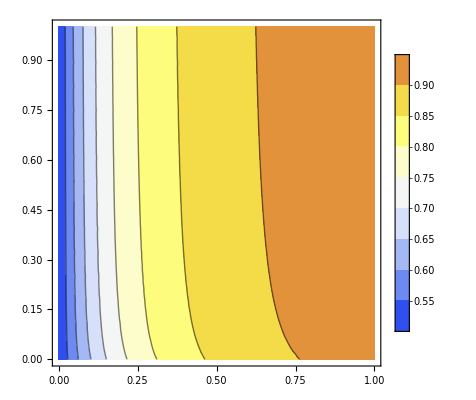
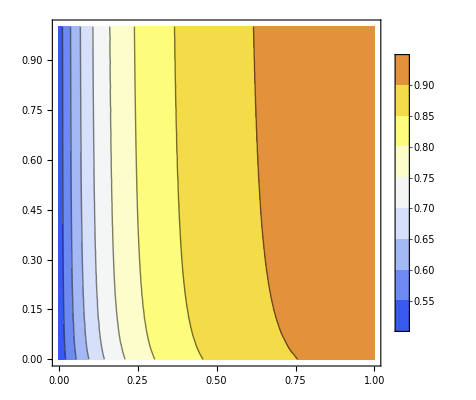
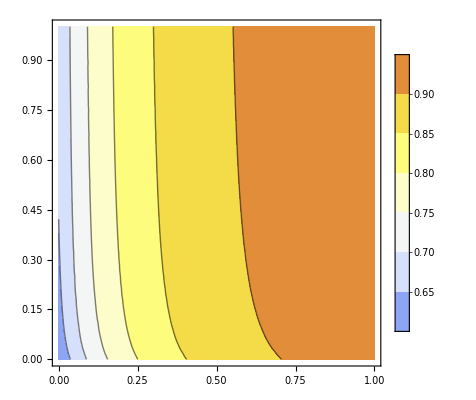

```mathematica
s2 = Table[ContourPlot[
scen1Ub[par2, par1, 0.14,  0.14, 0.14, bAH][[1,1,2]],
{par1,0.,1.},{par2,0.,1.}, ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0.5, 1.0}}], PlotLegends->Automatic], {bAH, {0., 1/100, 1/10}}]
```

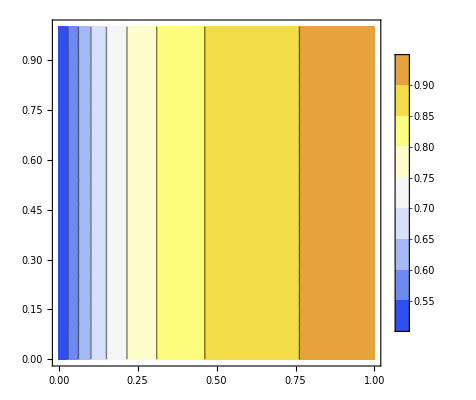
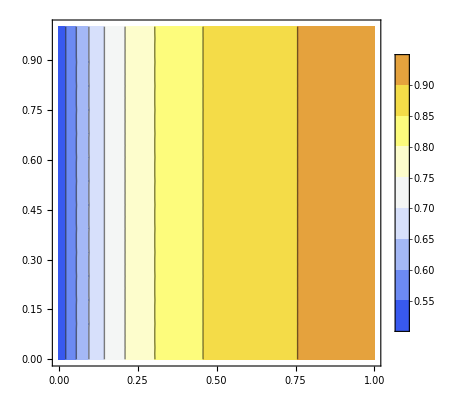
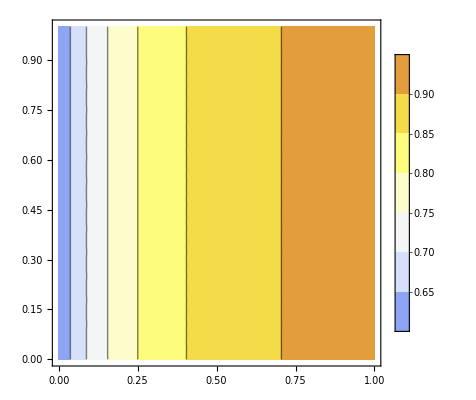
Row[-Graphics-,-Graphics-,-Graphics-]

```mathematica
s3 = Table[ContourPlot[
scen1Ub[0., par1, 0.14,  0.14, 0.14, bAH][[1,1,2]],
{par1,0.,1.},{par2,0.,1.}, ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0.5, 1.0}}], PlotLegends->Automatic], {bAH, {0., 1/100, 1/10}}
s2 = ContourPlot[
scen1Ub[0., par1, 0.14,  0.14, 0.14, 1/100][[1,1,2]],
{par1,0.,1.},{par2,0.,1.}, ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0.5, 1.0}}], PlotLegends->Automatic];
s3 = ContourPlot[
scen1Ub[0., par1, 0.14,  0.14, 0.14, 1/10][[1,1,2]],
{par1,0.,1.},{par2,0.,1.}, ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0.5, 1.0}}], PlotLegends->Automatic];
Row[s1, s2, s3]
```

```mathematica
(*RE(A) / RE*)
animalfrac[Rs_] := Rs[[1]]/Rs[[2]]
sol1[LA_, bAH_, bEH_, bEA_, bHE_, bAE_] := NSolve[{Unboundfrac[[1]]==0, Unboundfrac[[2]]==0, Unboundfrac[[3]]==0, Unboundfrac[[4]]==0, Unboundfrac[[5]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0 && z[t]≥ 0&& r[t]≥ 0} /.{Subscript[Λ, H]->1/10,Subscript[Λ, A]->LA, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, AH]->bAH,Subscript[β, HA]->1/1000, Subscript[β, EH] ->bEH,  Subscript[β, EA]->bEA, Subscript[β, HE] -> bHE, Subscript[β, AE] -> bAE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] ->1/5}, {x[t], y[t], w[t], z[t], r[t]}, Reals]
```

```mathematica
Row[
ContourPlot[animalfrac[sol1[par2, 1/1000, par1, 0.14, 0.14, 0.14][[1,{5,3},2]]], {par1, 0., 1.}, {par2, 0., 1.},FrameLabel->{Style["β_EH", 32],Style["Λ_A",32]}, PlotLegends->Automatic],
ContourPlot[animalfrac[sol1[par2, 1/1000, 0.14, par1, 0.14, 0.14][[1,{5,3},2]]], {par1, 0., 1.}, {par2, 0., 1.}, FrameLabel->{Style["β_EA", 32],Style["Λ_A",32]},PlotLegends->Automatic, PlotRange->All],
ContourPlot[animalfrac[sol1[par2, 1/1000, 0.14, 0.14, par1, 0.14][[1,{5,3},2]]], {par1, 0., 1.}, {par2, 0., 1.}, FrameLabel->{Style["β_HE", 32],Style["Λ_A",32]},PlotLegends->Automatic],
ContourPlot[animalfrac[sol1[par2, 1/1000, 0.14, 0.14, 0.14, par1][[1,{5,3},2]]], {par1, 0., 1.}, {par2, 0., 1.}, FrameLabel->{Style["β_AE", 32],Style["Λ_A",32]},PlotLegends->Automatic]]
```

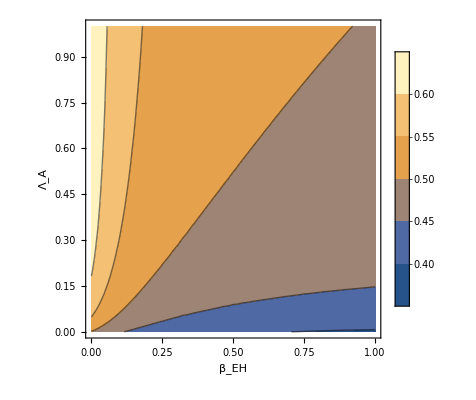
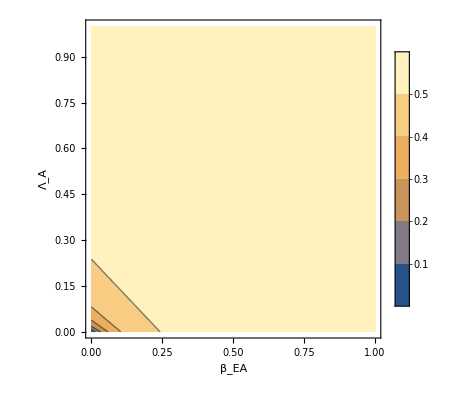
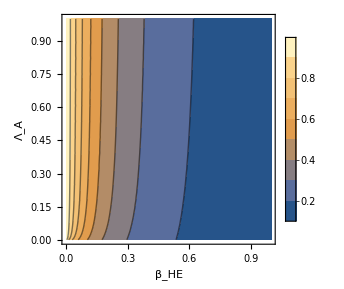
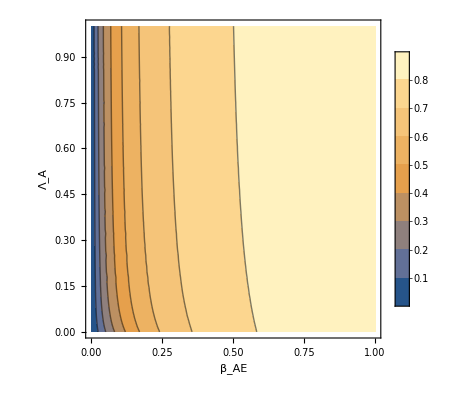
```mathematica
Row[-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

```mathematica
sol1[0.1, 1/1000, 0.14, 0.14, 0.14, 0.14][[1,{5,3},2]]
```

{0.494548,0.989096}

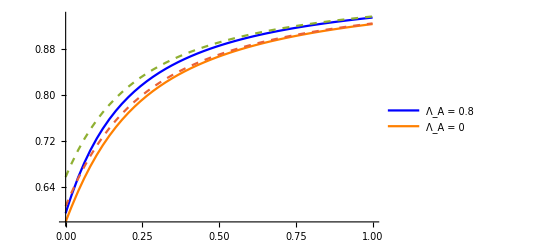

```mathematica
Plot[{scen1Ub[0.8, par1, 0.14, 0.14, 0.14, 0.05][[1,1,2]], scen1Ub[0., par1, 0.14, 0.14, 0.14, 0.07][[1,1,2]], scen1Ub[0.8, par1, 0.14, 0.14, 0.14, 0.1][[1,1,2]], scen1Ub[0., par1, 0.14, 0.14, 0.14, 0.1][[1,1,2]]}, {par1, 0., 1.0}, PlotStyle -> {Blue, Orange, Dashed, Dashed}, PlotLegends->{"Λ_A = 0.8", "Λ_A = 0"}]
```

```mathematica
Manipulate[Plot[{scen1Ub[0.8, par1, 0.14, 0.14, 0.14, bAH][[1,1,2]], scen1Ub[0., par1, 0.14, 0.14, 0.14, bAH][[1,1,2]]}, {par1, 0., 1.0},PlotLegends->{"Λ_A = 0.8", "Λ_A = 0"}, PlotRange-> {{0., 1.0}, {0.5, 0.95}}], {bAH, 0., 0.1}]
```

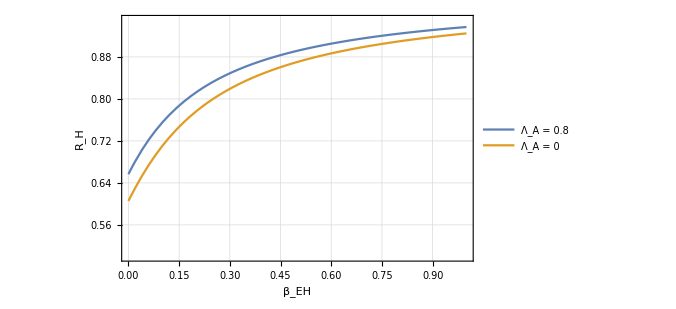

```mathematica
Plot[{scen1Ub[0.8, par1, 0.14, 0.14, 0.14, 0.1][[1,1,2]], scen1Ub[0., par1, 0.14, 0.14, 0.14, 0.1][[1,1,2]]}, {par1, 0., 1.0}, PlotLegends->{"Λ_A = 0.8", "Λ_A = 0"}, PlotTheme->{"Detailed"},PlotRange->{{0.,1.0},{0.5, 0.95}},  FrameLabel->{"β_EH", "R_H"}, LabelStyle->Directive[Bold, Large],ImageSize->500]
```

```mathematica
(*Find parameter range where RH ~71% is maintained*)

sol1[bOE_, bEO_] :=NSolve[{Unbounded[[1]]==0., Unbounded[[2]]==0., Unbounded[[3]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, EH] ->bEO, Subscript[β, EA]-> bEO, Subscript[β, HE] ->bOE, Subscript[β, AE] ->bOE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0.1,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals]
sol2[bA_, bH_] := NSolve[{Unbounded[[1]]==0., Unbounded[[2]]==0., Unbounded[[3]]==0.&& x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0. } /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, EH] ->bH, Subscript[β, EA]-> bA, Subscript[β, HE] ->bH, Subscript[β, AE] ->bA, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0.1,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals]

sol3[bOE_, bEO_] :=NSolve[{Bounded[[1]]==0., Bounded[[2]]==0., Bounded[[3]]==0. && x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0.} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, EH] ->bEO, Subscript[β, EA]-> bEO, Subscript[β, HE] ->bOE, Subscript[β, AE] ->bOE, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0.1,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals]
sol4[bA_, bH_] := NSolve[{Bounded[[1]]==0., Bounded[[2]]==0., Bounded[[3]]==0.&& x[t] ≥ 0. && y[t] ≥ 0. && w[t] ≥ 0. } /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->1/1000,Subscript[β, HH]-> 1/1000, Subscript[β, AA]-> 1/1000,Subscript[β, EH] ->bH, Subscript[β, EA]-> bA, Subscript[β, HE] ->bH, Subscript[β, AE] ->bA, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/5, Subscript[Λ, A]->0.1,Subscript[Λ, H]->1/10, Subscript[γ, A]-> 1/1000, Subscript[γ, H]-> 1/1000}, {x[t], y[t], w[t]}, Reals]
```

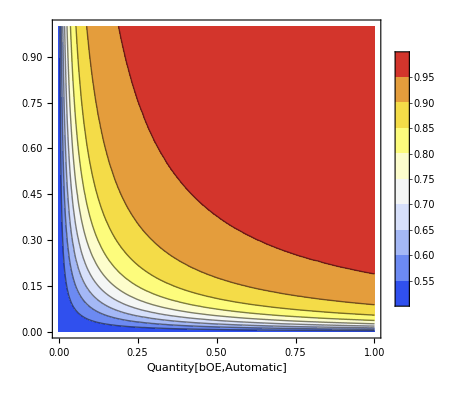

```mathematica
ContourPlot[sol1[bOE, bEO][[1,1,2]], {bOE, 0., 1.}, {bEO, 0., 1.},ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap", {0.5, 1.0}}], Contours=2, PlotLegends->Automatic, FrameLabel->True]
```

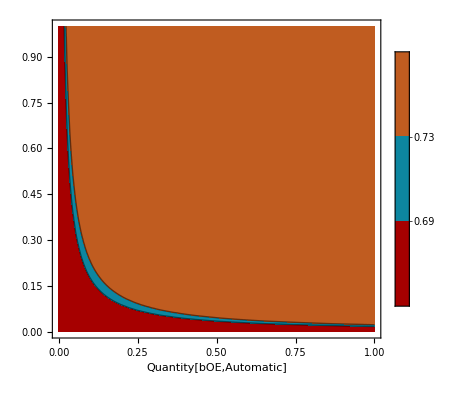
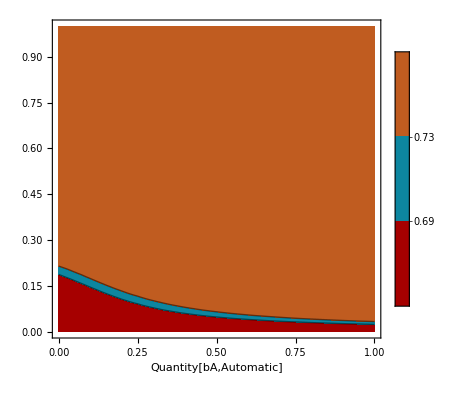
Row[-Graphics-,-Graphics-]

```mathematica
Row[ContourPlot[sol1[bOE, bEO][[1,1,2]], {bOE, 0., 1.}, {bEO, 0., 1.},Contours-> {0.69,0.73}, PlotLegends->Automatic, FrameLabel->True, ContourShading->ColorData[99,"ColorList"]], ContourPlot[sol2[bA, bH][[1,1,2]], {bA, 0., 1.}, {bH, 0., 1.},Contours-> {0.69,0.73}, PlotLegends->Automatic, FrameLabel->True, ContourShading->ColorData[99,"ColorList"], PlotRange-> All]]
```

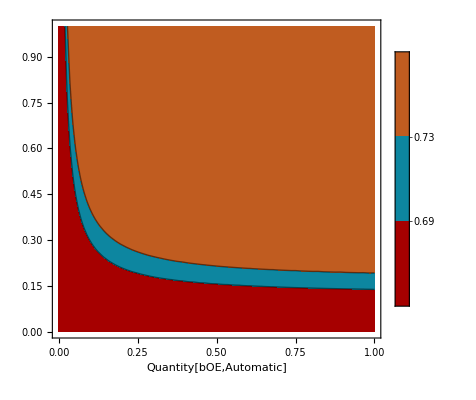
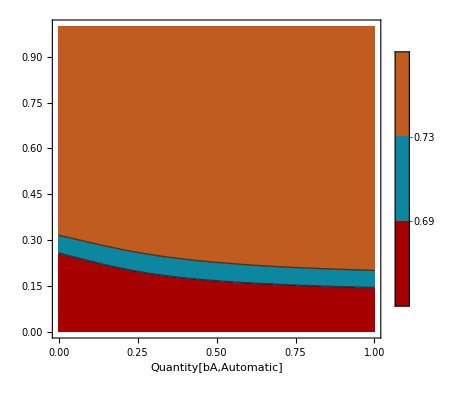
Row[-Graphics-,-Graphics-]

```mathematica
Row[ContourPlot[sol3[bOE, bEO][[1,1,2]], {bOE, 0., 1.}, {bEO, 0., 1.},Contours-> {0.69,0.73}, PlotLegends->Automatic, FrameLabel->True, ContourShading->ColorData[99,"ColorList"]], ContourPlot[sol4[bA, bH][[1,1,2]], {bA, 0., 1.}, {bH, 0., 1.},Contours-> {0.69,0.73}, PlotLegends->Automatic, FrameLabel->True, ContourShading->ColorData[99,"ColorList"], PlotRange-> All]]
```

```mathematica
Timing[Table[sol1[0.1, 0.1], {i, 1000}]]
```

{7.07813,{{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},990,{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}},{{x[t]→0.620308,y[t]→0.620308,w[t]→0.621308}}}}
 |  |  |  |